```mathematica
wordCountFromPath[path_String?FileExistsQ] := WordCount@Import@path;
sentenceCountFromPath[path_String?FileExistsQ] := Length@TextSentences@Import@path;
```

```mathematica
statsFromPath[path_String?FileExistsQ] := With[{text = Import@path}, {WordCount[text], Length[TextSentences[text]]}];
randSentences[path_String?FileExistsQ, randNum_:3] := With[{text = Import@path},Span[TextSentences[text],Random]];
```

```mathematica
folder = "/Users/AaronLopes/Desktop/newsela_article_corpus/articles/";

metadata = Import[
	"/Users/AaronLopes/Desktop/newsela_article_corpus/articles_metadata.csv",
	"Dataset",
	"HeaderLines" -> 1
	];

enMetadata = metadata[Select[#language=="en"&]];
refEasyGrouped = Normal@GroupBy[enMetadata, {#slug&, If[#gradelevel ≤ 6.0, "easy", "hard"]&}];

(* Change second parameter for randlist to select number of random files *)
sample = RandomSample[refEasyGrouped, 10];
sample = Map[RandomChoice, sample, {2}];
(*^ randomly choose one file in easy and one in hard: bug if one level is empty!*)

sampleFilePath = Map[
	Map[FileNameJoin[{folder, #}]&]@
		{#[["hard", "filename"]], #[["easy", "filename"]]}&
	, sample
	];

hardeasywc = Map[wordCountFromPath, sampleFilePath, {2}];
hardeasystats = Map[statsFromPath, sampleFilePath,{2}];
```

```mathematica
(*partition analysis*)
```

```mathematica
sentAnalysis[path_String?FileExistsQ] :=
```

```mathematica
easytexts = Import[#]&/@Values[sampleFilePath[[All, 1]]];
hardtexts = Import[#]&/@Values[sampleFilePath[[All, 2]]];
easysent = TextSentences@easytexts;
hardsent = TextSentences@hardtexts;
easysentences
positions = Sort@RandomInteger[Min[Length[easysentences[[1]]],Length[hardsentences[[1]]]], 5]

Grid[Transpose[{easysent[[All, positions]],hardsent[[All, positions]]}], Frame-> All]
```

{{MIAMI, Fla. — President Barack Obama on Wednesday paid his first visit to the Everglades to deliver an Earth Day speech.,He spoke about the threat of rising seas at the endangered national park and the risk of climate change across the nation.,But his choice of South Florida clearly had a political reason, as well.,Voters will elect Obama's successor in 18 months, and the Republican candidates for president, including one from Florida, question whether climate change is man-made.,They have taken this position despite significant scientific research concluding that climate change is mainly caused by pollution from fossil fuels like oil.,In a speech delivered at Everglades National Park, the president also got a subtle dig in at Florida Governor Rick Scott, who has come under fire after he ordered state workers to avoid using the term "climate change.","Climate change can no longer be denied … cannot be edited out of the conversation," Obama said.,The Republican governor, who declined an invitation to join Obama on his Everglades tour, has denied that state workers are forbidden to use the term.,## The River Of Grass,Before his speech, the president and park rangers walked the Anhinga Trail, the park's most popular tourist stop.,They passed baby alligators, sleek cormorants and a pair of black vultures, which are famous for occasionally eating the rubber off visitors' vehicles.,Obama said he could think of "no better place" to spend Earth Day than the River of Grass, as the Everglades is called.,He praised the virtues of the Everglades, remarking that it provides a habitat for both alligators and crocodiles.,"I'm told this is a good thing," he joked.,The president was also in South Florida to speak about his administration's record on tackling environmental problems.,Most notably, it has limited carbon emissions, the pollution many scientists say causes climate change, and spent $2.2 billion on projects to restore the Everglades.,Obama was expected to reveal new conservation efforts in four areas of the country, including Southwest Florida.,And in a move some say is long overdue, the National Park Service will designate Marjory Stoneman Douglas' cottage in Florida as a national monument.,Douglas is a pioneering preservationist whose book, "Everglades: River of Grass," inspired restoration efforts.,## In Senator Rubio's "Backyard",Obama's decision to focus on climate change in South Florida also could have implications on the presidential campaign.,It could pressure Republicans to debate the subject, which is a touchy one for the Republican Party.,Among the climate-change skeptics is presidential candidate Republican Senator Marco Rubio of Florida.,A trip to Rubio's backyard to warn about climate change will hardly go unnoticed in the early days of the 2016 campaign.,"This is not an effort necessarily to go to anybody's home state," White House press secretary Josh Earnest told reporters Tuesday.,"The truth is those Republicans that choose to deny the reality of climate change, they do that to the detriment of the people that they're elected to represent," Earnest said.,Governor Scott on Tuesday called on the federal government to speed up funding to Everglades restoration projects.,The White House admits that the government has owed the project money since even before Obama took office.,The state has invested $1.9 billion in the Comprehensive Everglades Restoration Project, nearly a billion dollars more than the federal government.,Scott said in a statement that Obama must find a way to give Florida the $58 million the government still owes.,"President Obama needs to live up to his commitment on the Everglades," Scott said.,"This has caused critical maintenance delays in the Everglades to linger for over a year.",## Slow Death Of The Everglades?,Earnest suggested that Scott make the funding request to the Republican-controlled Congress.,He said the governor's criticism was over the top given that Scott's government is avoiding even the use of the term "climate change.",Obama's visit comes at a critical time for Everglades restoration, which has dragged on for nearly 15 years.,Last November, Florida voters overwhelmingly to buy land for restoration projects.,Yet state lawmakers balked at using the money to buy about 46,000 acres.,Restoration work is also becoming more critical as the rising seas begin taking a toll on the wetlands.,This week, scores of scientists revealed new research that showed even more dramatic changes caused by climate change could occur in the future.,A United Nations group predicts increases in temperature, sea level and ocean salinity.,Mangrove forests, which provide protection against extreme storms and floods in the Everglades, could disappear, studies found.,The soil will become more salty, which would allow the ocean to flood the Everglades, shrinking it.,The wetlands of the Everglades, which provides much of South Florida's freshwater, are already half their original size.,"We're at this key moment where there's crucial public recognition" of the effects of global warming, said Florida International University ecologist Evelyn Gaiser, who has been invited to meet with Obama after his speech.,She said awareness of the slow death of the Everglades could be a model for other natural areas endangered by climate change around the world.},{![](//newsela-test-files-f331e.s3.amazonaws.com/uploads/20130829_TEENJOBS.jpg) WASHINGTON — U.S. teen employment stayed stuck around record lows for the fourth consecutive summer, leading experts to fear that a generation of youth will face a future of lower earnings and less opportunity.,The trend is all the more striking given that the overall unemployment rate has steadily dropped, to 7.4 percent in August.,And employers in recent months have been collectively adding almost 200,000 new jobs a month.,It had led to hopes that this would be the summer when teen employment improved.,In 1999, slightly more than 52 percent of teenagers 16 to 19 worked a summer job.,But by this year, that number had plunged to about 32.25 percent over June and July.,It means that slightly more than 3 in 10 teens actually worked a summer job.,There are about 16.8 million teenagers in the United States.,"We have never had anything this low in our lives.,This is a Great Depression for teens, and no time in history have we encountered anything like that," said Andrew Sum, director of the Center for Labor Market Studies at Northeastern University in Boston.,"That's why it's such an important story.",## Numbers Worse For Minorities,Summer is traditionally the peak period of employment for teens.,They are off from school and get their first brush with employment and the responsibilities that come with it.,But falling teen employment is just as striking in the 12-month numbers over the past decade.,These teen employment numbers looks even worse when broken down by race.,Sum and colleagues did just that, comparing June and July 2000 and the same two months of 2013.,In 2000, 61.28 percent of white teens 16 to 19 held a job, a number that fell to 39.25 percent this summer.,For African-Americans, a number that was dismal in 2000, 33.91 percent of 16- to 19-year-olds holding a job, fell to a staggering low of 19.25 percent this June and July.,It wasn't terribly better for Hispanics, who saw the percentage of employed teens fall from 40.31 percent in the two-month period of 2000 to 26.7 percent in June and July 2013.,One of the more surprising findings of Sum's research is that teens whose parents were wealthy were more likely to have a job than those whose parents had less income.,Some 46 percent of white male teens whose parents earned between $100,000 and $149,000 held a job this summer.,Only 9.1 percent of black male teens whose family income was below $20,000 had a job.,And 15.2 percent of Hispanic male teenagers with that same low family income held a job.,That finding is important.,A large amount of research shows that teens who work do better in a wide range of social and economic indicators.,The plunging teen employment rate could mean trouble for this generation of young workers of all races.,## "A Huge Missed Opportunity","Kids that get work experience when they are 17 or 18 end up graduating from college at a higher rate," said Michael Gritton, executive director of the Workforce Investment Board.,The group promotes job creation and teen employment in Louisville, Ky., and six surrounding counties.,"There are economic returns to those young people because they get a chance to work.,Almost every person you ask remembers their first job because they started to learn things from the world of work that they can't learn in the classroom," Gritton explained.,The teen employment numbers are calculated by the U.S. government.,The weak employment numbers sometimes prompt people to say that younger workers are just staying in college longer rather than entering the workforce, or are going on to graduate school given the impaired jobs market.,But that idea is mistaken, experts say.,"I think there is this myth out there that there is some silver lining for young people, that they are going on to college.,You don't see an increase in enrollment rates over and above the long-term trend.,You can't see a Great Recession blip," said Heidi Shierholz, a labor economist at the liberal Economic Policy Institute, a research group.,"They are not in school.,There's been a huge spike in the not-in-school, not employed.,It's just a huge missed opportunity.",## Losing Jobs To Older Workers,Even before the economic crisis exploded in the summer of 2008, workers aged 16 to 19 made up a declining share of the overall workforce.,Part of the reason was a decades-long climb in college enrollment.,Another part was that universities now place less importance on work and more on life experiences and community service.,But most of this decline of youth in the workforce is thought to be the result of the severe economic crisis and its aftermath.,Older workers have been taking the jobs of teens.,"People entering into the labor force in their 20s, it looks like more and more now they're not going to have any work experience as teens.,Labor force participation is as low as it's ever been," said Keith Hall.,He served as commissioner of the U.S. Bureau of Labor Statistics from 2008 to 2012.,Hall points to a troubling trend within an already worrisome statistic.,Because of the so-called Great Recession and the sluggish growth that's followed, middle-age and older workers are not moving up the career ladder.,"I think that means that a lot of workers aren't advancing through their careers," he said.,"Younger workers aren't going to be progressing through their careers as they did before."},{CHICAGO — On a recent afternoon at Chicago's Dewey Elementary Academy of Fine Arts, Ladon Brumfield asked a group of 9- and 10-year-old African-American girls to define beauty.,The nearly 20 girls unanimously agreed that if a woman had short, kinky hair, she was not beautiful.,But when Brumfield, the director of a project empowering young girls, passed around a photograph of Lupita Nyong'o, the dark-brown-skinned actress who sports an extra-short natural, the girls were silent for a moment.,Then, once again, their answer was unanimous: They agreed Nyong'o was beautiful.,"It's like they had to make a mental readjustment," said Brumfield, founder of the non-profit Girls Rule!,"This was in conflict with the overwhelming imagery they receive from the media about having to have long hair.",For more than a decade, increasing numbers of black women have been wearing their natural hair in Afros, braids, locks and twists.,But now, thanks in part to Nyong'o, it's the TWA, or teenie weenie Afro, that's getting a second look and expanding notions of beauty into territory where it really hasn't taken root before — the larger culture.,Nyong'o isn't the first black woman or celebrity to sport a super-short natural.,Actresses Viola Davis and Danai Gurira have done so, along with model Alek Wek and singer Grace Jones.,But what's different about Nyong'o is that she's been embraced outside the black community as both media darling and graceful beauty.,On Friday.,Nyong'o was named the new face of Lancome cosmetics.,Experts say that extra-short hair will have to go to great lengths to overcome many of today's issues surrounding beauty and hair that reach back to slavery.,But it may give more women who have been contemplating the "big chop" the confidence to do so.,"Even when we were wearing Afros during the 'I'm black and I'm proud' (period of the 1960s and 70s), people said, 'Who has the bigger Afro?' and length was an issue," said journalist and black hair historian A'Lelia Bundles, 61.,She's the great-great-granddaughter of black hair care magnate Madam C.J. Walker.,"Hair is considered our crown and glory, and women view it as an expression of selfhood.,But as we get older and become more secure in ourselves, hair often is just hair.","For a lot of black women, hair is an accessory, but they're also looking for validation," said Tonya Roberts, who studies multicultural trends at the Chicago office of market researcher Mintel.,"When things become acceptable to society, it's a wink to (the black community) that it's OK — especially if the question is: Will I be able to get a job with this hairstyle?,Will my co-workers or family members accept me?",As part of a national survey Mintel released last year on black hair care, the company asked black women to rate six different hair styles shown in photographs.,The styles included hair that was braided, long and straight, short and straight, natural, long and curly, and locked.,Roberts said that although women considered hair that was long and straight and long and curly to be "high maintenance," they deemed the styles "healthy," "sexy" and "professional.",Short hair, which Mintel defined as about jaw-length, was considered the most "professional" and "classy" of all the styles.,And natural hair was viewed as being low maintenance while conveying confidence.,All of the styles were considered attractive.,"We didn't ask about the teenie-weenie Afros because a couple of years ago people weren't talking about them the way they are today," Roberts said, adding that the firm plans to ask about the style in this year's survey.,Throughout history, long hair has been viewed as a marker of beauty and femininity among various cultures.,But length has been elusive for some black women, whose hair texture can range from straight to wavy to curly to kinky, because the natural coil of the hair makes it appear shorter.,Women who have desired longer hair have depended on hair straightening products, hot combs, flat irons, weaves, extensions and wigs.,Frances Simmons, a natural hair care professional who visits Chicago public schools to talk to students about proper hair care, said she's not against women getting weaves or extensions that are woven in properly.,But too many girls are getting them at a very young age and at the expense of healthy hair and a healthy self-image.,"I've met a lot of girls who prefer some type of hair contraption, rather than their own because they feel hair has to be long to be beautiful," said Simmons.,"It doesn't matter if the fake hair is matted and cheap and braids (are) falling off.,What does that say about our self-esteem and self-worth?",Lanita Jacobs, a University of Southern California associate professor of Anthropology and American Studies and Ethnicity, has written about the politics of black hair, and why length and texture matter so much to women of color in this country and around the world.,"We grew up stretching our curls out and saying, 'See this is how long my hair really is,'" said Jacobs, who's black and wears her hair in a short Afro.,"Length is always somewhere in the room unless you take it out the equation and go in the opposite direction, and that's what Lupita and others are doing.",Encouraging people to embrace short hair has long been a challenge in a media environment overflowing with images of women whose hair is "bouncing and behaving," said Aeleise Jana, 30, a Chicago hair stylist who wears her hair short and specializes in cutting natural hair.,She said that by the time her clients reach her, many have decided they've had enough of chemicals and weaves and their only prospect for a healthy head of hair is to cut most of it off.,"There was one woman who was wearing this plastic-looking wig and when she took it off, she had beautiful short, kinky hair that went with her cheekbones, but she was very uncomfortable wearing her own hair," said Jana.,"We're told that our hair is too nappy and too dry and too short and we've internalized those messages.",In 2008, it was Leila Noelliste's "big chop" that inspired her to found the popular Chicago-based "Black Girl With Long Hair" natural hair blog.,She had decided to stop flat-ironing her hair and wearing it in braided styles with extensions.,Despite its title, the blog celebrates natural hair of varying lengths.,"We think for black women, length should be a choice and that's what we're trying to promote as a website and as a community," said Noelliste, 28, who loves her teenie weenie afro.,When Chicago resident Candace Peterson, 28, the co-founder of the Kiss My Curls blog, went natural and cut most of her hair off in 2011, she said she took in a barrage of negative feedback before she became confident about her hair.,"People would say things like, 'You look like Celie from 'The Color Purple.' Or, 'Your hair is too nappy.,How often do you comb it?' Or, 'You can't go out with me looking like that,'",Peterson said.,Peterson hopes Nyong'o will inspire girls to love their hair length and texture, and carry themselves with poise.,"Lupita's look is something I'd never seen before (as a standard of beauty) in Hollywood," said Peterson.,"Maybe I'm an optimist, but I hope she represents a shift.,You never know what will make a difference in a child's life.,Maybe by seeing someone who looks like her, she can feel more self-assured and brave."},{LOS ANGELES — It has long been known that the clouds of gas and dust, or nebulae, that dying stars cast off are strikingly colorful.,Now, though, astronomers have discovered something new and mysterious: Some planetary nebulae in the Milky Way galaxy's central bulge are strangely aligned.,The discovery was made by two University of Manchester astrophysics researchers, who will publish their findings shortly in Monthly Notices of the Royal Astronomical Society.,The new findings provide insight into how the stars behind the nebulae formed.,And they also suggest what unknown forces near the Milky Way's heart could have pulled the nebulae into formation.,A dying star's nebula is a sight to behold.,Like a flower shedding its petals, an aging star casts off its outer layers, surrounding itself with cloud-like shells of gas and dust.,These ethereal structures are created by stars with masses of about one to eight suns, and are often rendered in breathtaking color.,Stars that are more massive than eight suns tend to explode into supernovae.,But these shells aren't just interstellar eye candy.,Planetary nebulae can tell scientists much about the environment in which they were formed.,Nebulae reflect their stars' individual characteristics.,And they can reveal whether a star is one of a binary pair of stars and whether it has any orbiting planets tugging at it gravitationally.,## Something Strange In Galactic Bulge,The two researchers, lead author Bryan Rees and Albert Zijlstra, studied data from 130 nebulae.,All are located roughly 26,000 light-years away in the Milky Way's densely populated central galactic bulge.,About 44 of them were bipolar;,that is, they had formed into twin gas clouds, often resembling butterfly wings.,The majority were elliptical, meaning they had a mostly roundish shape.,Soon the researchers began to notice something strange: More than half of the bipolar nebulae seemed to be aligned, even though they were separated by vast distances of many light-years amid the crowded galactic bulge.,Just one light year equals about 6 trillion miles.,"The surprise is that there's a relationship between things that are so widely separated," Rees said.,"Now, how can we explain it?",Other bipolar nebulae that sit closer to the Earth, farther from the galactic center, are randomly oriented, not neatly arranged.,This means there must be something going on in the bulge that's causing its nebulae to line up.,The nebulae's shared alignment points to "a powerful magnetic pull in the galactic bulge when they were formed," Rees said.,"It's not necessarily there now.",## Strong Magnetic Fields At Play,Say you're holding a magnet near a bunch of scattered nails, and only some of the nails are magnetized.,Only the magnetized nails will turn and point if you bring the magnet near, leaving the unmagnetized ones untouched.,That's sort of what could be happening here, astronomers say.,The bipolar nebulae were probably two-star systems with strong magnetic fields.,Like the magnetized nails, they would have been unable to resist a powerful magnetic force in the galactic bulge around when it was forming stars, about 8 to 13 billion years ago.,The elliptical nebulae, lacking this strong magnetic field, remained unmoved.,If you were to look at these bipolar nebulae along the plane of the galaxy, Rees said, they would look like hourglasses lying on their sides.,The findings could help explain how "bipolar nebulae are formed, and provide some insight, possibly, on the way the bulge was formed," he said.,The study doesn't go into what exactly could have caused that magnetic field.,However, a recent study in Nature says it has found evidence for a strong magnetic field around the black hole at the center of the Milky Way.,Whether that field could have extended to where these nebulae are, and had the observed effect, remains to be seen.},{BREEZY POINT, N.Y. — The sky is cloudless and blue in this coastal community of bungalows by the sea.,But Stephanie Abrams has disaster on her mind.,A meteorologist with the Weather Channel, Abrams is here to co-host the network's morning shows to kick off the start of hurricane season.,Her employer is predicting more storms this usual this year.,Abrams has come to this town, which was walloped by Hurricane Sandy last year, to warn viewers of potential dangers in the months ahead.,"It only takes one — one Sandy or Katrina in order for the entire U.S. or the entire world to feel that hurt and pain," she said, looking into the camera.,Seconds later, viewers watching the show live on TV saw a scary graphic of a gazebo battered by wind and rain.,The station proclaimed itself Hurricane Central.,Bad weather is good business for the Weather Channel.,Helped by a steady string of blizzards, tropical storms, hurricanes and tornadoes, the cable channel has increased its revenue while some other media outlets have struggled.,Even when the weather in most of the country is mild, the channel's round-the-clock coverage tends to be heavy with big graphics, capital letters and warnings of what bad weather could be unfolding somewhere, soon, in the United States.,Such weather data are now expanding to the Web and cellphones, part of the reason the company changed its name to the Weather Co. from the Weather Channel late last year.,But as storms get fiercer and more frequent, the Weather Channel has come under fire for covering them in a way that seems more entertainment than information.,It decided last year to start giving names to winter storms, a unilateral move that drew ire from meteorologists and the National Weather Service, which is responsible for naming hurricanes.,Its coverage of "Nemo," the snowstorm that blanketed much of the East Coast in February, featured all-caps headlines such as "YOU MUST PREPARE NOW," links that allowed people to warn their friends that bad weather was coming, and graphics of snow and wind that more aptly depicted the Ice Age than a snowstorm.,The gossip site Gawker poked fun at the breathless coverage in an article with the headline "Snow Panic Has Driven Weather.com Completely Insane.",Still, big storms are catnip for advertisers.,The fourth quarter of the 2012, which included Sandy and some other big winter storms, was a blockbuster, said Curt Hecht, chief global revenue officer for Weather Co., which is privately held.,Weather.com had more page views on the first day of Sandy than NBC.com had for all of the London Olympics, he said.,"It's hard to say, 'Boy, we made a lot of money' … when people have lost their homes," Hecht said.,"But the reality is Sandy, from a hurricane perspective, was our largest ad monetization event.",The week of Hurricane Sandy, it averaged 780,000 viewers in the heavily viewed 6 to 10 a.m. time slot, more than double the previous week, according to the ad firm Horizon Media.,To keep up with viewer demand for big weather events, the company has added two experts to its severe-weather team over the last year.,Technology allows it to air more and more footage from big storms across the U.S. and around the world.,It has also beefed up its website, which now has 1.5 billion monthly page views, with feature stories and photo galleries that are only tangentially weather-related ("Before the Bikini: Rare Vintage Beach Photos").,NBC joined two private equity firms to buy the Weather Channel in 2008, and since then weather shows have increasingly featured cross-promotions with other NBC properties, including segments from CNBC.,The Weather Channel started airing more reality shows and television programs such as "Deadliest Space Weather" and "Forecasting the End," running 11 series in 2012 and launching 15 this year.,"Forecasting the End," according to promotional materials, is about how "catastrophic weather or natural disasters could possibly cause the end of days.",A "Did You Know" section on the show's website warns viewers that "one fiery spark" of methane gas "could ignite global destruction.",That's a big departure from the Weather Channel's early days.,The channel was founded in 1982 as a way to bring localized forecasting information to viewers across the country.,It pitched itself as a necessity for viewers trying to plan their days who needed to know what kind of weather they might encounter.,The channel's new emphasis on what some derisively refer to as "weather porn" has probably alienated some viewers.,"I can't watch the Weather Channel anymore — it's just like Froot Loops fed to you," said Carson Glover, a wannabe meteorologist in New York.,"They have pictures of lawn chairs tipped over, it gets people needlessly anxious, and then it just feeds on itself," he said.,But with consumers increasingly turning to weather websites and mobile apps for their daily forecasts, the Weather Channel had to give viewers something different, said Brian Wieser, an analyst with Pivotal Research Group.,"They had to evolve as weather was becoming much more commoditized — you could get forecasts from all different types of sources," he said.,The Weather Co. makes around $350 million a year, a 15 percent jump from five years ago, according to SNL Kagan, a media research company.,Meanwhile, its programming expenses have risen 20 percent, to about $165 million, which is relatively low compared with those of other channels.,Longtime viewers seem divided over the company's new direction.,On the Weather Channel's Facebook page, some commenters say they are fascinated by promotions for new series, while others urge the channel to return to weather coverage and put aside original programming.,"I am captivated by the excitement &amp; adventurous &amp; scientific explanations of these Historic Events.,Love it!!!!" wrote one viewer.,"I am old.,I remember when the Weather Channel actually was weather coverage 24/7/365 not this crap they put on now," wrote another.,But executives say that viewers are becoming more interested in weather as they see destruction from storms such as Sandy and Katrina and wonder whether they'll be seeing more extreme events like them soon.,"Weather is kind of a primal force in the world — it's fundamental to everybody," said David Kenny, chairman and chief executive of the Weather Co. "Seeing Mother Nature in action is fundamentally interesting — who doesn't marvel at the power of nature, even though it's terrible, threatening and fear-inducing?",The company's first goal is to prepare people who are in the line of danger from storms, Kenny said.,But it also wants to explain the weather and show its ferocity to viewers.,"There is more extreme weather, there are more unusual patterns, and as we've been able to film it more, it's a more interesting story," he said.,That might be part of the struggle the Weather Co. faces as it moves forward.,It may be tough to both inform people about the weather and highlight the dangerous nature of storms without exaggerating their danger to the average viewer.,For instance, a video recently on the website, "Inside Tumbling TWC Video," shows the inside of a Weather Channel truck that got dangerously close to the El Reno tornado in Oklahoma and was rolled around by the wind.,Meteorologist Mike Bettes suffered minor injuries from the event.,Three storm chasers who had appeared on the Discovery Channel died in the same storm.,Though the tornado was more unpredictable than most, many viewers of the Weather Channel were able to stay safe by heeding its warnings and going to a shelter, rather than driving toward the storm.,They didn't need up-close footage of the tornado to do so.,"There's a lot of anecdotal evidence that certain stations put a guy on the beach to get good visuals, but it's not necessarily the smartest thing to do," said Jeffrey Lazo, an economist with the National Center for Atmospheric Research, who studies the public's demand for weather forecasts.,"It can be hard to separate the hype from the public service part.",Back at Breezy Point, Abrams has tried to inform viewers about how to prepare for hurricanes each time she has been on the air.,She interviews the local fire chief about how candles can start fires, encourages people to have flashlights rather than candles, warns inland residents about the dangers of inland flooding and tells coast dwellers to send their family photos away during hurricane season.,She's not trying to scare anyone but wants to prepare them, Abrams said.,"I think it's all in the tone and the way you present it," she said.,"A lot of it is in the delivery."},{NEW YORK — Want a side salad with that Big Mac?,Now, you might be able to get one.,McDonald's says it will start giving customers the choice of a salad, fruit or vegetable as a substitute for french fries in its value meals.,McDonald's Corp. will roll out the change early next year in the United States, where people will be able to pick a salad instead of fries at no extra cost.,McDonald's says it already lets customers make such swaps in some countries, such as France.,But now it says it will work to make the options available in 20 of its biggest markets around the world.,Those 20 countries represent 85 percent of the company's sales.,McDonald's, which has more than 34,000 locations around the world, said the change will be in place in 30 to 50 percent of the areas within the next three years and all the regions by 2020.,## "We Really Want Consumption",The world's biggest hamburger chain made the announcement at the Clinton Global Initiative in New York City.,McDonald's CEO Don Thompson made an appearance on stage with former President Bill Clinton.,In an interview before the announcement, Thompson said McDonald's is looking at developing other healthy sides that will appeal to customers.,He noted that the company could also take the fruits and vegetables it offers in other parts of the world, such as cups of corn and kiwi on a stick, and make them more widely available.,"What is it that customers will choose, and what will they eat?",Thompson said.,"What we don't want to do is just put something on the menu and say, hey, we did it.,We really want consumption.",McDonald's also announced that it would use its packaging to make healthier options more appealing to kids.,For example, a side of carrots might come in a more colorfully designed bag.,Parents will still be able to order soda with Happy Meals, but McDonald's says it will only promote milk, juice and water on menu boards and in its ads.,All advertising to kids will include a "fun nutrition or children's well-being" message, the company said.,## Shaking Its Fast-Food Image,Margo Wootan is the director of nutrition policy at the health advocacy group Center for Science in the Public Interest.,She said taking soda off the menu as an option for Happy Meals was a big step that other fast-food chains should follow.,But she said the push to include positive nutrition messages in ads to kids could serve to give McDonald's a "health halo" that it doesn't necessarily deserve.,"The changes McDonald's are making make the food somewhat healthier.,But I don't think a hamburger, some apples and fries is something I'd call healthy," she said.,The announcement comes as McDonald's faces criticism from health advocates who say it promotes bad eating habits.,After years of outperforming its rivals, McDonald's is also struggling to shake its fast-food image and keep up with shifting tastes.,Late last year, the company reported its first monthly sales decline in nearly a decade.,Sales performance around the world has been choppy ever since.,To better reflect the way people are eating, McDonald's recently started giving customers the choice to substitute egg whites in all its breakfast sandwiches.,It also rolled out chicken wraps, which are partly intended to go after people who want foods they feel are fresher or healthier.,Earlier in the week, rival Burger King rolled out lower-calorie french fries, reflecting the growing demand for better-for-you options.,## Changing The Way People Eat?,McDonald's marketing to children is also an ongoing issue.,A recent study by the Robert Wood Johnson Foundation, for example, found that the chain's ads targeting children often emphasize toy giveaways and movie tie-ins, rather than food.,And at its latest annual shareholders meeting, a 9-year-old girl made headlines after she stood to ask Thompson to stop "tricking" kids into eating the company's food.,The girl was with her mother, who was affiliated with Corporate Accountability.,The group has pressured McDonald's to change its marketing practices to kids.,The criticism is clearly a sensitive topic for Thompson, who noted that the Alliance for a Healthier Generation approached the company to use its "marketing might" to help kids.,The group, which is working with McDonald's on its new health goals, was founded by the Clinton Global Initiative and the American Heart Association.,"Others have said, 'McDonald's, don't advertise to kids,'",Thompson said.,"We've always felt like, wow, if we had the impact that you think we have, why don't we leverage it to do something great for kids?",Howell Wechsler, CEO of Alliance for a Healthier Generation, said the commitments made by McDonald's were worked out over the course of more than a year.,He said the final agreement could help change the way people eat over time, given McDonald's enormous reach.},{BALTIMORE — Professor James Gates delivers his big ideas in simple but striking terms.,For example, this is what he says about setting lax standards for schoolchildren in science classes: It's like teaching them to dunk a basketball on a 9-foot-high hoop, when kids the next town over play with one 10 feet high.,Gates is a physicist — that is, he studies the nature of matter and energy.,More specifically, he is a theoretical physicist, which means that he uses math to test his hypotheses about matter, motion and how the universe came to be.,He has colorful opinions not only about science teaching, but about his fellow scientists as well.,## Groundbreaking Ideas In Physics,Without diversity of thought among scientists working together, Gates says, you get nothing but classical music.,There is little innovation without different types of people working together.,"When you let different people create different music, you get things like rock 'n' roll, jazz," Gates said.,"I have a particular kind of individualized viewpoint about the way mathematics I do should work.",His research at the University of Maryland, College Park focuses on translating that complicated math into something digestible for other scientists and the rest of us.,Much of his work seeks to replace messy equations with a relatively simple set of pictures and diagrams.,Gates gets a lot of attention because he has groundbreaking ideas in the field of physics, and he is able to explain his ideas better than anyone else.,Last year, he received a National Medal of Science from the National Science Foundation.,Last month, the Harvard Foundation bestowed on him the title of Scientist of the Year.,He sits on both the state school board and the President's Council of Advisers on Science and Technology.,Gates is about as famous as a theoretical physicist can get.,In a popular video by the PBS show "Nova," he attempts to explain a complicated theory called string theory in 30 seconds.,These days, Gates is continuing his own work in physics.,At the same time, he is also making efforts to ensure young scientists can pick up where he leaves off.,"Most scientists, we get busy with our own work.,Not many take the time to spread it at a level that is" understandable for "the general public," said Professor Jogesh Pati.,"Jim has great strength in doing it.,Beautifully, he does it.",## Field Of Supersymmetry,Gates' work is devoted to simplifying the complicated.,His specialty is something called supersymmetric string theory.,This seeks to mesh the two major branches of physics, Einstein's theory of relativity and quantum mechanics, into a single set of rules governing the universe.,The former takes in the vastness of space and time to explain gravity;,the latter focuses on the rules guiding atomic and subatomic phenomena.,The 63-year-old's interest in the physics of things was sparked by a science fiction movie he saw as a small boy and a book on space travel his father brought home.,Before delving into a career in physics, he nearly became an astronaut.,Eventually, he settled on the field of supersymmetry.,To make an important contribution, all scientists need to tread into new territory.,Gates, however, stands out for his ability to lead others along his path, those who work with him say.,"He sees things in a geometric way," said physicist Martin Rocek.,This approach "is a way that allows you to visualize things" — to see them in your mind's eye.,"That makes things more understandable.",One of Gates' first important papers was "Superfield supergravity" in 1979, a collaboration with physicist Warren Siegel.,Rocek recalled that Siegel had some provocative and original ideas in papers he had published on his own, "but nobody understood them at all.",When Gates joined Siegel on the 1979 paper, he clarified the ideas enormously.,Since then, the work has been used by others hundreds of times.,As the ideas caught on in the physics community, Pati and others took notice.,Pati began pushing to lure Gates from Massachusetts Institute of Technology (MIT), where he was then teaching, to Maryland.,"I actually pleaded with the department that we should hire him, and they agreed," Pati said.,## String Theory In 30 Seconds,Since coming to College Park in 1984, Gates has taught classes nearly every semester.,He first learned of his fondness for teaching while tutoring members of MIT's Black Student Union.,Back then, many black students still didn't feel comfortable asking teachers for help, Gates said.,"To me that was really exciting, to get that light to turn on in their eyes," Gates said.,Students who have listened to his lectures said Gates' style is illuminating.,This is thanks to his ability to explain broader connections and the bigger picture.,Gates' responsibility extends far beyond his own students, however.,In 2009, Gov. Martin O'Malley chose him to help schoolchildren statewide.,"Maryland is, as far as I can tell, the only state in the country that has a theoretical physicist on its board of education," Gates said.,Gates' powers of explanation also have helped him bring science to general audiences.,As part of a "Nova",TV series called "The Secret Life of Scientists and Engineers," he lays out in half a minute the idea behind string theory — or most of it.,"I tried," he says at the end.,In another Nova program, he lays out a lofty standard for success — that "I will, by the end of my career, have done something of value for our species.",Science, he said, is the foundation for the technology that improves our lives.,Ultimately, it is what may save us from [global warming](https://www.newsela.com/?tag=global+warming) and other perils.},{LOS ANGELES, Calif.,— Before she joined the after-school gardening program at her inner-city Los Angeles high school, Elizabeth Castro had never even tasted beets or kumquats.,Now, the 15-year-old doesn't just eat these things.,She also grows them on her school campus, in a garden bigger than a football field, smack in middle of a gritty city neighborhood.,"Instead of going home and doing nothing at all, we come here," Castro said.,Besides learning about new foods herself, she has also taken samples home for her family to try.,## U.S. Surgeon General Pays A Visit,"Many things that I experienced here, I had never experienced before," Castro told Surgeon General Vivek Murthy when he toured the 1.5 acre site.,The surgeon general is the top doctor in the United States and is appointed by the government to oversee matters of public health in the country.,Murthy visited the garden, which is a partnership between community organizations and John C. Fremont High School.,He wanted to give support to this unique program that helps deal with weight issues in children and the lack of availability of fresh produce where they live.,"These kinds of programs, they help build a demand for healthy foods," Murthy said.,## Students Learn To Grow, Prepare Food,At the South Los Angeles campus, students involved in the 12-week after-school gardening apprenticeship program learn to grow food.,They also learn to cook healthy dishes, using the kumquats and limes, potatoes, peas and beets that they grow themselves.,The Los Angeles Neighborhood Land Trust is a group that works to create parks and gardens in Los Angeles.,It partnered with the school to start the garden four years ago and plans to soon add a greenhouse.,Mark Glassock, who is director of special projects for the Trust, said the students have seen improvement not just in terms of nutrition, but also in their grades.,He would like to see more schools adopt similar programs.,"Schools have a lot of property on their campuses, much of which is underutilized, so this is a great alternative to use that space," he said.,## Fruits, Vegetables Can Reduce Obesity,A 2013 report showed about 40 percent of Fremont High School's students were overweight or obese, Glassock said.  That is higher than the national average.,Obesity is the condition of being severely overweight and can lead to serious health problems, including heart disease.,Across the country, about 17 percent of children ages 2 to 19 are obese, according to the Centers for Disease Control and Prevention (CDC), a government agency in charge of protecting the health and safety of Americans.,Studies show that eating more fresh fruits and vegetables is an important way of fighting weight problems.,Azucena Lozoya, 16, said she signed up for the gardening program because she never had a chance to try anything like it before.,Since then, she has enjoyed tasting kale and a variety of melons.,Such foods are new additions to the rice, bean and chicken dishes she usually gets at home, she said.,"My mom never makes stuff like that," Lozoya said.,"This helps us have a different range of food.,This helps us have choices."},{CHICAGO — Up wooden steps, past unlit Christmas lights dangling in the window, Dr. Fred Richardson Jr. walked through the doorway of Louise Cannon's house on a cold late fall night on Chicago's West Side.,He passed Cannon's grandchildren, a photo of the Obamas on the mantel and a statuette of the Virgin Mary, then pulled back curtains to a dining room converted to a makeshift hospital room.,Unable to speak after a series of strokes, Cannon, 79, was in bed.,A rerun of "Good Times" glowed on the TV in a corner.,She saw Richardson, raised her emaciated left arm and beamed.,"How are you, Miss Cannon?",Richardson asked, taking her hand.,"All right, sweetheart.,Now I'm going to check your breathing, OK?",She cooed.,A son of the Englewood neighborhood on Chicago's South Side, Richardson has been a solo practitioner of family medicine since 1990.,Throughout that time, he has been doing what he did on that Tuesday night: grabbing his scuffed, black, leather bag and making house calls primarily in the city's most dangerous neighborhoods.,Richardson also has become a legacy builder, rescuing minority students struggling with medical school by bringing those students — many on probation;,some dismissed outright — into the small waiting room of his west suburban Oak Park storefront office three days a week.,There Richardson, 54, teaches them the practical applications of what they are trying to grasp in textbooks.,It's known as problem-based learning, and Richardson does it without financial compensation.,"He's our brightest light," said John Bradley, an administrator at Chicago Area Health and Medical Careers Program, which identifies promising minority students for medical careers, advocates for them in medical schools and supports them academically.,By Bradley's count, Richardson has saved 50 of those students from leaving medical school.,"He's got more medical student saves than anybody doing this kind of work," Bradley said.,"He's tremendous.",It was more than 30 years ago, but Richardson still recalls the question from an interviewer screening applicants to Rush Medical College in 1982.,How did Richardson know he wanted to be a doctor?,He had no black physician role models who would make for a tidy answer.,His mother was a bookkeeper;,his father a construction worker who struggled with alcoholism.,The family moved frequently.,Richardson remembers spending a night in a shelter.,"I like 'M*A*S*H*,'",Richardson told the interviewer, a reference to the long-running TV show about a mobile military surgical unit.,"I love Alan Alda.",His other medical idol?,"Marcus Welby, MD," a 1960s and '70s TV drama starring the very Caucasian Robert Young as a family physician.,He made house calls, which looked heroic to Richardson.,Those small screen heroes are part of a somewhat complicated explanation for why Richardson does what he does.,His Christian faith also factors into it.,But all of it starts with his mother, Gladys Richardson.,Though the family moved often, they resided around 63rd Street and Wolcott Avenue, an area of low income and high unemployment and crime.,Gladys carried the financial load for the family, somehow keeping her four kids in Catholic schools.,"Her goal in life was to educate her children because she thought that was the only way out of Englewood," Richardson said over breakfast at a pancake house down the street from his office, "and so she was a strict disciplinarian;,stressed academics; stressed excellence.",Homework was a serious undertaking.,Straight A's were expected.,Anything less and Gladys Richardson could resort to corporal punishment.,"If the grades weren't there, she was ...",Richardson's voice trailed off, then he chuckled.,"There was just not much flexibility there at all.",That approach was her way of making sure her four children avoided the destructive path many young people took in Englewood.,Despite her sometimes harsh discipline, Richardson said he felt overwhelming love from his mother.,As a student at St. Rita High School, Richardson was assigned to read Mark Twain's "Pudd'nhead Wilson" and found it impenetrable.,Gladys Richardson sat with him all night, translating every page.,While his neighborhood friends "were into all sorts of bad things," they protected him and his younger brother, Lendell, who also became a physician.,Playing baseball frequently in the neighborhood gained them wide acceptance, Richardson recalled, and their focus on becoming doctors was respected by those friends.,"They were like, 'OK, don't mess with them because they may have to take care of us,'",Richardson said.,He arrived at St. Rita in 1974 and had dreams of playing shortstop for the Cubs.,But Richardson stood about 5 feet 4 inches — even with an auspicious Afro that earned him the nickname Freddie Fro — and was cut from the school teams as a freshman and sophomore.,He knew then, Richardson said, that academics was his path.,He graduated in the top three of his class, earned an academic scholarship to Loyola University in Chicago and met Julie Ann Llorens, a pre-med student at Loyola, on a Chicago Transit Authority elevated train.,The two were married June 15, 1985.,At St. Rita, he was one of about four African-American students.,When he was admitted to Rush University's medical school, Richardson recalled, he was the only African-American male in his class.,The volume of material overwhelmed Richardson, forcing him to study 12 hours a day.,To get through it, Richardson said, he leaned on the example his mother set.,Gladys encouraged her son at an early age to be an orthopedic surgeon, which would enable him to treat his father's bone disease.,But at Rush he soon discovered orthopedics was not for him, and was intrigued by family medicine.,During his residency, Richardson worked with Dr. Stephen Humowiecki, who made house calls.,Now retired, Humowiecki recalled a "very outgoing" resident who was kind to patients and collegial to residents.,Richardson had a reputation for lightening dire settings.,"He was someone who was very interested in learning and naturally attuned to helping the whole person," Humowiecki said.,"Everyone liked working with him.",In 24 years of house calls, Richardson says, he's never been hassled in the neighborhoods.,"Part of it is having grown up in an area like this," he said after leaving Cannon's home in the Garfield Park neighborhood.,Richardson drove a gleaming black 2015 Mercedes;,wore a white doctor's coat over a dress shirt and trim, striped tie.,"I'm not intimidated by this at all," he said of the neighborhood.,"None of this bothers me.",Ten minutes after finishing his work with Louise Cannon, Richardson and his wife, who manages the practice and accompanies him to all house visits, arrived at the home of 95-year-old Alberta Bowles, who lives alone in a two-bedroom brick house a few blocks from Cannon.,He asked about her shortness of breath, whether she has had more belly problems.,He gently massaged her hands, asked if they hurt.,"One of the things I enjoy the most about having a doctor like Dr. Fred is that he's a good listener," Bowles said.,"You can talk to him.,He does not rush you to do anything and he never dismisses anything you say.","He is," she added, "the son I didn't have.",Richardson works six days a week and is on call 24 hours a day, seven days a week.,He says he sleeps four hours a night, doesn't drink alcohol or coffee and avoids carbohydrates to deal with his diabetes.,He sips diet cola all day.,"I think what makes you tick is the impact you have on lives," Richardson said one night in his office.,He was battling a cold.,He will continue making house calls, he said, because it allows him to connect with people in ways he cannot do in an office or hospital.,He'll hang on to his solo practice, too, which he said makes no money.,He views it in part as a haven for helping "under-represented" medical students.,Richardson navigates a health care landscape that quakes with change.,Flat reimbursements to physicians, rising costs and competition from retail clinics are pushing doctors to consolidate practices and affiliate with hospitals.,House calls, which reached a high of 40 percent of patient encounters in 1930, nearly disappeared by 1980, research shows.,Since then, the number of house visits has climbed.,An analysis of Medicare shows that 4.5 million house calls per year are billed to the federal health care provider, up from 1.1 million in 1984.,Part of that rise stems from evidence that treating an individual at home avoids the high cost of hospitalizations, experts say.,Richardson handles the challenges by working as an employee physician of Little Company of Mary Hospital in suburban Evergreen Park, where he sees patients through the afternoon before going to his family practice and treating patients through the evening.,That's also when he makes house calls.,When he returns to the office shortly after 8 p.m., a cluster of medical school students often is seated in his waiting room.,Two decades ago, Clyde Whiting was one of those students.,He described Richardson "teasing out" textbook lessons, helping students assemble the puzzle pieces.,"I think that without that at that particular time," Whiting said, "I could have been lost.,I could have fallen through the cracks for sure.",Today, he is an emergency room physician.,Richardson is Whiting's personal doctor.,Gladys Richardson, now in her late 70s, suffered a stroke about a year ago and struggles to speak.,Fred Richardson cited that complication in declining to allow her to comment for this story.,His father died about a decade ago.,At the November wedding reception of his oldest daughter, serving a residency in family medicine, Gladys danced a little.,Richardson used his father-of-the-bride speech to remind people where celebrations like this start.,"This started at 63rd and Wolcott in Englewood," Richardson recalled saying, "and it started with my mom making sure that I did my homework.,And, now my daughter's a physician.,I wanted my mom to take a bow for that.",But paths to celebrations like that can start in millions of places, even in Louise Cannon's home, with her 2-year-old great-great-granddaughter, Bri'elle Brewster.,On that Tuesday night house call, Bri'elle flitted and chirped while watching Richardson check Cannon's blood pressure and her hearing.,When he finished, Bri'elle stepped in his path.,Richardson bent, pulled his stethoscope from his neck and let Bri'elle listen to her heartbeat.,Then she held her doll to Richardson, who pressed the stethoscope's chest piece to the doll's chest.,She listened.,"There you go," Richardson said.,"You could be a doctor someday."},{WASHINGTON — Tens of thousands of people from across the nation gathered at the National Mall Saturday to commemorate the 50th anniversary of the March on Washington and to rally for what they believe is the unfinished business of the civil rights battle.,Under picture-perfect blue skies, the throng assembled around the base of the Lincoln Memorial — where Martin Luther King Jr. delivered his iconic "I Have a Dream" speech — and listened to speaker after speaker implore them to become active participants, not bystanders, in the quest of racial equality and harmony.,Rep. John Lewis, D-Ga., the only living speaker from the 1963 march, fired up Saturday's crowd by exhorting them to fight against the Supreme Court's decision last June that struck down a key provision of the Voting Rights Act of 1965.,"I gave a little blood on that bridge in Selma, Ala.," he told the crowd, referring to the 1965 "Bloody Sunday" march from Selma to Montgomery, Ala., in which protestors were brutally beaten on the Edmund Pettus Bridge.,"I got arrested 40 times during the '60s, beaten and left bloodied and unconscious . . . But I'm not tired.,I am ready to fight and continue to fight, and you must fight.",Attorney General Eric Holder echoed his sentiments, saying Saturday's event was "about far more than reflecting on our past.","This morning, we must affirm that this struggle must, and will, go on in the cause of our quest for justice — until every eligible American has the chance to exercise his or her right to vote, unencumbered by discriminatory or unneeded procedures, or practices.,It must go on until our criminal justice system can ensure that all are treated equally and fairly in the eyes of the law.",As the morning of oratory moved along, more and more people seemed to make their way to the Mall.,The National Park Service, which is in charge of the Mall, doesn't provide crowd size estimates.,In their planning for the event, District of Columbia officials said they were expecting at least 700 55-passenger charter buses from out of town.,Hilary Shelton, director of the NAACP's Washington bureau, estimated that more than 100,000 people were on the Mall by noon on Saturday.,The mood and atmosphere around the Lincoln Memorial were festive and reflective as people sat on blankets or on lawn chairs and cheered as speakers made their points.,Many young people and adults wore T-shirts or buttons, or carried signs protesting the acquittal of George Zimmerman in the shooting death of Florida teenager Trayvon Martin.,Vendors hawked March on Washington anniversary paraphernalia, goods with Trayvon Martin's likeness, and buttons and T-shirts signifying President Barack Obama's two elections.,Emma Daniels, 70, wore a cap adorned with buttons from the 1963 march.,Standing under a shady tree with her family, Daniels pointed to where she and other members of Augusta, Ga.'s Tabernacle Baptist Church stood 50 years ago when they made the bus journey to Washington.,"I wanted my children to have the same feeling that I had — change," said Daniels, who now lives in Lorton, Va. "We came out here to march for change, we can't stay home.,We've seen a lot of change, we're going forward, it's slow, but we're moving forward.",Daniels said she noticed a different atmosphere Saturday than what she experienced in the Aug. 28, 1963, march.,She said she remembers there being an air of tension then, mainly because many of the 250,000 people who were there that day had traveled through a segregated South and feared being stopped by inhospitable law enforcement officers along the way.,"This is so much more relaxed than when we came up — like a family reunion," she said.,Melanie Marshall, 34, Daniels' daughter, said the Saturday's event gave her a greater appreciation for the right to assemble.,"In Egypt, people are fighting and killing each other in the street," she said.,"We're lucky to be able to come together like this, in a peaceful way.",Amber Brown, 43, made the five-hour drive from Raleigh, N.C., to Washington with her two children to witness Saturday's events because she wanted her children to learn about "American history and the fact that there are people who fought and died to give them the opportunity to do whatever they want to do and be whatever they want to be.",Darryl Simmons, 21, made the bus journey to Washington with fellow students from Orangeburg, S.C.'s Claflin University because "I just wanted to relive history.","We're not exactly dealing with what happened 50 years ago, but there's stuff going on and we're here for justice," said Simmons, president of Claflin's Young Democrats.,Saturday's commemoration was a prelude to Wednesday, Aug. 28, the March on Washington's official anniversary.,Another large crowd is expected at the Lincoln Memorial that day as Obama will speak at the spot where King made history 50 years ago.,The nation's first African-American president is expected to discuss the progress and problems the nation has faced in pursuit of [King's dream](http://www.archives.gov/press/exhibits/dream-speech.pdf) that his children "will one day live in a nation where they will not be judged by the color of their skin but by the content of their character.",Obama rarely talks directly about race, but in the days after the Martin shooting verdict he delivered a sometimes personal analysis as to why Zimmerman's acquittal struck a chord within the African-American community.,Perhaps offering a preview of Wednesday's speech, Obama opened up again on Friday at a town hall meeting at New York's Binghamton University when Anne Bailey, an associate professor of African-American history and African Diaspora studies, asked him where he thought the nation stood 50 years after King's speech.,"Fifty years after the March on Washington and the 'I Have a Dream' speech, obviously we've made enormous strides," Obama told Bailey.,"I'm a testament to it.,The diversity of this room and the students who are here is a testimony to it.,And that impulse towards making sure everybody gets a fair shot is one that found expression in the Civil Rights movement, but then spread to include Latinos and immigrants and gays and lesbians.",Yet, Obama said the legacy of discrimination, including slavery and segregationist Jim Crow laws, means that "some of the institutional barriers for success" still exist.,He noted that African-American poverty in the United States is still significantly higher than for other groups, along with Latinos and Native Americans.,He said it's in "all our interest to make sure that we are putting in place smart policies to give those communities a lift.","Unfortunately, we've got politics sometimes that divides instead of bringing people together," Obama said, adding that there is a "tendency to suggest somehow that government is taking something from you and giving it to somebody else, and your problems will be solved if we just ignore them or don't help them.,And, that, I think, is something that we have to constantly struggle against — whether we're black or white or whatever color we are."}}

{14,29,30,39,41}

Part::partw: Part {14,29,30,39,41} of {LOS ANGELES — It has long been known that the clouds of gas and dust, or nebulae, that dying stars cast off are strikingly colorful.,«37»,Whether that field could have extended to where these nebulae are, and had the observed effect, remains to be seen.} does not exist.

Part::partw: Part {14,29,30,39,41} of {NEW YORK — McDonald's is the world's biggest hamburger restaurant company.,It has more than 34,000 restaurants around the world.,But there's a problem.,«33»,She stood up at a McDonald's company meeting.,She asked Thompson to stop "tricking" kids.} does not exist.

Transpose::nmtx: The first two levels of {{«1»}⟦All,{14,29,30,39,41}⟧,{{MIAMI, Fla. — President Barack Obama spoke about climate change during his first visit to the Florida Everglades Wednesday.,He said the global threat is putting the national park in danger.,«48»,«7»},«9»}⟦All,{14,29,30,39,41}⟧} cannot be transposed.

Grid[Transpose[{{{MIAMI, Fla. — President Barack Obama on Wednesday paid his first visit to the Everglades to deliver an Earth Day speech.,He spoke about the threat of rising seas at the endangered national park and the risk of climate change across the nation.,But his choice of South Florida clearly had a political reason, as well.,Voters will elect Obama's successor in 18 months, and the Republican candidates for president, including one from Florida, question whether climate change is man-made.,They have taken this position despite significant scientific research concluding that climate change is mainly caused by pollution from fossil fuels like oil.,In a speech delivered at Everglades National Park, the president also got a subtle dig in at Florida Governor Rick Scott, who has come under fire after he ordered state workers to avoid using the term "climate change.","Climate change can no longer be denied … cannot be edited out of the conversation," Obama said.,The Republican governor, who declined an invitation to join Obama on his Everglades tour, has denied that state workers are forbidden to use the term.,## The River Of Grass,Before his speech, the president and park rangers walked the Anhinga Trail, the park's most popular tourist stop.,They passed baby alligators, sleek cormorants and a pair of black vultures, which are famous for occasionally eating the rubber off visitors' vehicles.,Obama said he could think of "no better place" to spend Earth Day than the River of Grass, as the Everglades is called.,He praised the virtues of the Everglades, remarking that it provides a habitat for both alligators and crocodiles.,"I'm told this is a good thing," he joked.,The president was also in South Florida to speak about his administration's record on tackling environmental problems.,Most notably, it has limited carbon emissions, the pollution many scientists say causes climate change, and spent $2.2 billion on projects to restore the Everglades.,Obama was expected to reveal new conservation efforts in four areas of the country, including Southwest Florida.,And in a move some say is long overdue, the National Park Service will designate Marjory Stoneman Douglas' cottage in Florida as a national monument.,Douglas is a pioneering preservationist whose book, "Everglades: River of Grass," inspired restoration efforts.,## In Senator Rubio's "Backyard",Obama's decision to focus on climate change in South Florida also could have implications on the presidential campaign.,It could pressure Republicans to debate the subject, which is a touchy one for the Republican Party.,Among the climate-change skeptics is presidential candidate Republican Senator Marco Rubio of Florida.,A trip to Rubio's backyard to warn about climate change will hardly go unnoticed in the early days of the 2016 campaign.,"This is not an effort necessarily to go to anybody's home state," White House press secretary Josh Earnest told reporters Tuesday.,"The truth is those Republicans that choose to deny the reality of climate change, they do that to the detriment of the people that they're elected to represent," Earnest said.,Governor Scott on Tuesday called on the federal government to speed up funding to Everglades restoration projects.,The White House admits that the government has owed the project money since even before Obama took office.,The state has invested $1.9 billion in the Comprehensive Everglades Restoration Project, nearly a billion dollars more than the federal government.,Scott said in a statement that Obama must find a way to give Florida the $58 million the government still owes.,"President Obama needs to live up to his commitment on the Everglades," Scott said.,"This has caused critical maintenance delays in the Everglades to linger for over a year.",## Slow Death Of The Everglades?,Earnest suggested that Scott make the funding request to the Republican-controlled Congress.,He said the governor's criticism was over the top given that Scott's government is avoiding even the use of the term "climate change.",Obama's visit comes at a critical time for Everglades restoration, which has dragged on for nearly 15 years.,Last November, Florida voters overwhelmingly to buy land for restoration projects.,Yet state lawmakers balked at using the money to buy about 46,000 acres.,Restoration work is also becoming more critical as the rising seas begin taking a toll on the wetlands.,This week, scores of scientists revealed new research that showed even more dramatic changes caused by climate change could occur in the future.,A United Nations group predicts increases in temperature, sea level and ocean salinity.,Mangrove forests, which provide protection against extreme storms and floods in the Everglades, could disappear, studies found.,The soil will become more salty, which would allow the ocean to flood the Everglades, shrinking it.,The wetlands of the Everglades, which provides much of South Florida's freshwater, are already half their original size.,"We're at this key moment where there's crucial public recognition" of the effects of global warming, said Florida International University ecologist Evelyn Gaiser, who has been invited to meet with Obama after his speech.,She said awareness of the slow death of the Everglades could be a model for other natural areas endangered by climate change around the world.},{![](//newsela-test-files-f331e.s3.amazonaws.com/uploads/20130829_TEENJOBS.jpg) WASHINGTON — U.S. teen employment stayed stuck around record lows for the fourth consecutive summer, leading experts to fear that a generation of youth will face a future of lower earnings and less opportunity.,The trend is all the more striking given that the overall unemployment rate has steadily dropped, to 7.4 percent in August.,And employers in recent months have been collectively adding almost 200,000 new jobs a month.,It had led to hopes that this would be the summer when teen employment improved.,In 1999, slightly more than 52 percent of teenagers 16 to 19 worked a summer job.,But by this year, that number had plunged to about 32.25 percent over June and July.,It means that slightly more than 3 in 10 teens actually worked a summer job.,There are about 16.8 million teenagers in the United States.,"We have never had anything this low in our lives.,This is a Great Depression for teens, and no time in history have we encountered anything like that," said Andrew Sum, director of the Center for Labor Market Studies at Northeastern University in Boston.,"That's why it's such an important story.",## Numbers Worse For Minorities,Summer is traditionally the peak period of employment for teens.,They are off from school and get their first brush with employment and the responsibilities that come with it.,But falling teen employment is just as striking in the 12-month numbers over the past decade.,These teen employment numbers looks even worse when broken down by race.,Sum and colleagues did just that, comparing June and July 2000 and the same two months of 2013.,In 2000, 61.28 percent of white teens 16 to 19 held a job, a number that fell to 39.25 percent this summer.,For African-Americans, a number that was dismal in 2000, 33.91 percent of 16- to 19-year-olds holding a job, fell to a staggering low of 19.25 percent this June and July.,It wasn't terribly better for Hispanics, who saw the percentage of employed teens fall from 40.31 percent in the two-month period of 2000 to 26.7 percent in June and July 2013.,One of the more surprising findings of Sum's research is that teens whose parents were wealthy were more likely to have a job than those whose parents had less income.,Some 46 percent of white male teens whose parents earned between $100,000 and $149,000 held a job this summer.,Only 9.1 percent of black male teens whose family income was below $20,000 had a job.,And 15.2 percent of Hispanic male teenagers with that same low family income held a job.,That finding is important.,A large amount of research shows that teens who work do better in a wide range of social and economic indicators.,The plunging teen employment rate could mean trouble for this generation of young workers of all races.,## "A Huge Missed Opportunity","Kids that get work experience when they are 17 or 18 end up graduating from college at a higher rate," said Michael Gritton, executive director of the Workforce Investment Board.,The group promotes job creation and teen employment in Louisville, Ky., and six surrounding counties.,"There are economic returns to those young people because they get a chance to work.,Almost every person you ask remembers their first job because they started to learn things from the world of work that they can't learn in the classroom," Gritton explained.,The teen employment numbers are calculated by the U.S. government.,The weak employment numbers sometimes prompt people to say that younger workers are just staying in college longer rather than entering the workforce, or are going on to graduate school given the impaired jobs market.,But that idea is mistaken, experts say.,"I think there is this myth out there that there is some silver lining for young people, that they are going on to college.,You don't see an increase in enrollment rates over and above the long-term trend.,You can't see a Great Recession blip," said Heidi Shierholz, a labor economist at the liberal Economic Policy Institute, a research group.,"They are not in school.,There's been a huge spike in the not-in-school, not employed.,It's just a huge missed opportunity.",## Losing Jobs To Older Workers,Even before the economic crisis exploded in the summer of 2008, workers aged 16 to 19 made up a declining share of the overall workforce.,Part of the reason was a decades-long climb in college enrollment.,Another part was that universities now place less importance on work and more on life experiences and community service.,But most of this decline of youth in the workforce is thought to be the result of the severe economic crisis and its aftermath.,Older workers have been taking the jobs of teens.,"People entering into the labor force in their 20s, it looks like more and more now they're not going to have any work experience as teens.,Labor force participation is as low as it's ever been," said Keith Hall.,He served as commissioner of the U.S. Bureau of Labor Statistics from 2008 to 2012.,Hall points to a troubling trend within an already worrisome statistic.,Because of the so-called Great Recession and the sluggish growth that's followed, middle-age and older workers are not moving up the career ladder.,"I think that means that a lot of workers aren't advancing through their careers," he said.,"Younger workers aren't going to be progressing through their careers as they did before."},{CHICAGO — On a recent afternoon at Chicago's Dewey Elementary Academy of Fine Arts, Ladon Brumfield asked a group of 9- and 10-year-old African-American girls to define beauty.,The nearly 20 girls unanimously agreed that if a woman had short, kinky hair, she was not beautiful.,But when Brumfield, the director of a project empowering young girls, passed around a photograph of Lupita Nyong'o, the dark-brown-skinned actress who sports an extra-short natural, the girls were silent for a moment.,Then, once again, their answer was unanimous: They agreed Nyong'o was beautiful.,"It's like they had to make a mental readjustment," said Brumfield, founder of the non-profit Girls Rule!,"This was in conflict with the overwhelming imagery they receive from the media about having to have long hair.",For more than a decade, increasing numbers of black women have been wearing their natural hair in Afros, braids, locks and twists.,But now, thanks in part to Nyong'o, it's the TWA, or teenie weenie Afro, that's getting a second look and expanding notions of beauty into territory where it really hasn't taken root before — the larger culture.,Nyong'o isn't the first black woman or celebrity to sport a super-short natural.,Actresses Viola Davis and Danai Gurira have done so, along with model Alek Wek and singer Grace Jones.,But what's different about Nyong'o is that she's been embraced outside the black community as both media darling and graceful beauty.,On Friday.,Nyong'o was named the new face of Lancome cosmetics.,Experts say that extra-short hair will have to go to great lengths to overcome many of today's issues surrounding beauty and hair that reach back to slavery.,But it may give more women who have been contemplating the "big chop" the confidence to do so.,"Even when we were wearing Afros during the 'I'm black and I'm proud' (period of the 1960s and 70s), people said, 'Who has the bigger Afro?' and length was an issue," said journalist and black hair historian A'Lelia Bundles, 61.,She's the great-great-granddaughter of black hair care magnate Madam C.J. Walker.,"Hair is considered our crown and glory, and women view it as an expression of selfhood.,But as we get older and become more secure in ourselves, hair often is just hair.","For a lot of black women, hair is an accessory, but they're also looking for validation," said Tonya Roberts, who studies multicultural trends at the Chicago office of market researcher Mintel.,"When things become acceptable to society, it's a wink to (the black community) that it's OK — especially if the question is: Will I be able to get a job with this hairstyle?,Will my co-workers or family members accept me?",As part of a national survey Mintel released last year on black hair care, the company asked black women to rate six different hair styles shown in photographs.,The styles included hair that was braided, long and straight, short and straight, natural, long and curly, and locked.,Roberts said that although women considered hair that was long and straight and long and curly to be "high maintenance," they deemed the styles "healthy," "sexy" and "professional.",Short hair, which Mintel defined as about jaw-length, was considered the most "professional" and "classy" of all the styles.,And natural hair was viewed as being low maintenance while conveying confidence.,All of the styles were considered attractive.,"We didn't ask about the teenie-weenie Afros because a couple of years ago people weren't talking about them the way they are today," Roberts said, adding that the firm plans to ask about the style in this year's survey.,Throughout history, long hair has been viewed as a marker of beauty and femininity among various cultures.,But length has been elusive for some black women, whose hair texture can range from straight to wavy to curly to kinky, because the natural coil of the hair makes it appear shorter.,Women who have desired longer hair have depended on hair straightening products, hot combs, flat irons, weaves, extensions and wigs.,Frances Simmons, a natural hair care professional who visits Chicago public schools to talk to students about proper hair care, said she's not against women getting weaves or extensions that are woven in properly.,But too many girls are getting them at a very young age and at the expense of healthy hair and a healthy self-image.,"I've met a lot of girls who prefer some type of hair contraption, rather than their own because they feel hair has to be long to be beautiful," said Simmons.,"It doesn't matter if the fake hair is matted and cheap and braids (are) falling off.,What does that say about our self-esteem and self-worth?",Lanita Jacobs, a University of Southern California associate professor of Anthropology and American Studies and Ethnicity, has written about the politics of black hair, and why length and texture matter so much to women of color in this country and around the world.,"We grew up stretching our curls out and saying, 'See this is how long my hair really is,'" said Jacobs, who's black and wears her hair in a short Afro.,"Length is always somewhere in the room unless you take it out the equation and go in the opposite direction, and that's what Lupita and others are doing.",Encouraging people to embrace short hair has long been a challenge in a media environment overflowing with images of women whose hair is "bouncing and behaving," said Aeleise Jana, 30, a Chicago hair stylist who wears her hair short and specializes in cutting natural hair.,She said that by the time her clients reach her, many have decided they've had enough of chemicals and weaves and their only prospect for a healthy head of hair is to cut most of it off.,"There was one woman who was wearing this plastic-looking wig and when she took it off, she had beautiful short, kinky hair that went with her cheekbones, but she was very uncomfortable wearing her own hair," said Jana.,"We're told that our hair is too nappy and too dry and too short and we've internalized those messages.",In 2008, it was Leila Noelliste's "big chop" that inspired her to found the popular Chicago-based "Black Girl With Long Hair" natural hair blog.,She had decided to stop flat-ironing her hair and wearing it in braided styles with extensions.,Despite its title, the blog celebrates natural hair of varying lengths.,"We think for black women, length should be a choice and that's what we're trying to promote as a website and as a community," said Noelliste, 28, who loves her teenie weenie afro.,When Chicago resident Candace Peterson, 28, the co-founder of the Kiss My Curls blog, went natural and cut most of her hair off in 2011, she said she took in a barrage of negative feedback before she became confident about her hair.,"People would say things like, 'You look like Celie from 'The Color Purple.' Or, 'Your hair is too nappy.,How often do you comb it?' Or, 'You can't go out with me looking like that,'",Peterson said.,Peterson hopes Nyong'o will inspire girls to love their hair length and texture, and carry themselves with poise.,"Lupita's look is something I'd never seen before (as a standard of beauty) in Hollywood," said Peterson.,"Maybe I'm an optimist, but I hope she represents a shift.,You never know what will make a difference in a child's life.,Maybe by seeing someone who looks like her, she can feel more self-assured and brave."},{LOS ANGELES — It has long been known that the clouds of gas and dust, or nebulae, that dying stars cast off are strikingly colorful.,Now, though, astronomers have discovered something new and mysterious: Some planetary nebulae in the Milky Way galaxy's central bulge are strangely aligned.,The discovery was made by two University of Manchester astrophysics researchers, who will publish their findings shortly in Monthly Notices of the Royal Astronomical Society.,The new findings provide insight into how the stars behind the nebulae formed.,And they also suggest what unknown forces near the Milky Way's heart could have pulled the nebulae into formation.,A dying star's nebula is a sight to behold.,Like a flower shedding its petals, an aging star casts off its outer layers, surrounding itself with cloud-like shells of gas and dust.,These ethereal structures are created by stars with masses of about one to eight suns, and are often rendered in breathtaking color.,Stars that are more massive than eight suns tend to explode into supernovae.,But these shells aren't just interstellar eye candy.,Planetary nebulae can tell scientists much about the environment in which they were formed.,Nebulae reflect their stars' individual characteristics.,And they can reveal whether a star is one of a binary pair of stars and whether it has any orbiting planets tugging at it gravitationally.,## Something Strange In Galactic Bulge,The two researchers, lead author Bryan Rees and Albert Zijlstra, studied data from 130 nebulae.,All are located roughly 26,000 light-years away in the Milky Way's densely populated central galactic bulge.,About 44 of them were bipolar;,that is, they had formed into twin gas clouds, often resembling butterfly wings.,The majority were elliptical, meaning they had a mostly roundish shape.,Soon the researchers began to notice something strange: More than half of the bipolar nebulae seemed to be aligned, even though they were separated by vast distances of many light-years amid the crowded galactic bulge.,Just one light year equals about 6 trillion miles.,"The surprise is that there's a relationship between things that are so widely separated," Rees said.,"Now, how can we explain it?",Other bipolar nebulae that sit closer to the Earth, farther from the galactic center, are randomly oriented, not neatly arranged.,This means there must be something going on in the bulge that's causing its nebulae to line up.,The nebulae's shared alignment points to "a powerful magnetic pull in the galactic bulge when they were formed," Rees said.,"It's not necessarily there now.",## Strong Magnetic Fields At Play,Say you're holding a magnet near a bunch of scattered nails, and only some of the nails are magnetized.,Only the magnetized nails will turn and point if you bring the magnet near, leaving the unmagnetized ones untouched.,That's sort of what could be happening here, astronomers say.,The bipolar nebulae were probably two-star systems with strong magnetic fields.,Like the magnetized nails, they would have been unable to resist a powerful magnetic force in the galactic bulge around when it was forming stars, about 8 to 13 billion years ago.,The elliptical nebulae, lacking this strong magnetic field, remained unmoved.,If you were to look at these bipolar nebulae along the plane of the galaxy, Rees said, they would look like hourglasses lying on their sides.,The findings could help explain how "bipolar nebulae are formed, and provide some insight, possibly, on the way the bulge was formed," he said.,The study doesn't go into what exactly could have caused that magnetic field.,However, a recent study in Nature says it has found evidence for a strong magnetic field around the black hole at the center of the Milky Way.,Whether that field could have extended to where these nebulae are, and had the observed effect, remains to be seen.},{BREEZY POINT, N.Y. — The sky is cloudless and blue in this coastal community of bungalows by the sea.,But Stephanie Abrams has disaster on her mind.,A meteorologist with the Weather Channel, Abrams is here to co-host the network's morning shows to kick off the start of hurricane season.,Her employer is predicting more storms this usual this year.,Abrams has come to this town, which was walloped by Hurricane Sandy last year, to warn viewers of potential dangers in the months ahead.,"It only takes one — one Sandy or Katrina in order for the entire U.S. or the entire world to feel that hurt and pain," she said, looking into the camera.,Seconds later, viewers watching the show live on TV saw a scary graphic of a gazebo battered by wind and rain.,The station proclaimed itself Hurricane Central.,Bad weather is good business for the Weather Channel.,Helped by a steady string of blizzards, tropical storms, hurricanes and tornadoes, the cable channel has increased its revenue while some other media outlets have struggled.,Even when the weather in most of the country is mild, the channel's round-the-clock coverage tends to be heavy with big graphics, capital letters and warnings of what bad weather could be unfolding somewhere, soon, in the United States.,Such weather data are now expanding to the Web and cellphones, part of the reason the company changed its name to the Weather Co. from the Weather Channel late last year.,But as storms get fiercer and more frequent, the Weather Channel has come under fire for covering them in a way that seems more entertainment than information.,It decided last year to start giving names to winter storms, a unilateral move that drew ire from meteorologists and the National Weather Service, which is responsible for naming hurricanes.,Its coverage of "Nemo," the snowstorm that blanketed much of the East Coast in February, featured all-caps headlines such as "YOU MUST PREPARE NOW," links that allowed people to warn their friends that bad weather was coming, and graphics of snow and wind that more aptly depicted the Ice Age than a snowstorm.,The gossip site Gawker poked fun at the breathless coverage in an article with the headline "Snow Panic Has Driven Weather.com Completely Insane.",Still, big storms are catnip for advertisers.,The fourth quarter of the 2012, which included Sandy and some other big winter storms, was a blockbuster, said Curt Hecht, chief global revenue officer for Weather Co., which is privately held.,Weather.com had more page views on the first day of Sandy than NBC.com had for all of the London Olympics, he said.,"It's hard to say, 'Boy, we made a lot of money' … when people have lost their homes," Hecht said.,"But the reality is Sandy, from a hurricane perspective, was our largest ad monetization event.",The week of Hurricane Sandy, it averaged 780,000 viewers in the heavily viewed 6 to 10 a.m. time slot, more than double the previous week, according to the ad firm Horizon Media.,To keep up with viewer demand for big weather events, the company has added two experts to its severe-weather team over the last year.,Technology allows it to air more and more footage from big storms across the U.S. and around the world.,It has also beefed up its website, which now has 1.5 billion monthly page views, with feature stories and photo galleries that are only tangentially weather-related ("Before the Bikini: Rare Vintage Beach Photos").,NBC joined two private equity firms to buy the Weather Channel in 2008, and since then weather shows have increasingly featured cross-promotions with other NBC properties, including segments from CNBC.,The Weather Channel started airing more reality shows and television programs such as "Deadliest Space Weather" and "Forecasting the End," running 11 series in 2012 and launching 15 this year.,"Forecasting the End," according to promotional materials, is about how "catastrophic weather or natural disasters could possibly cause the end of days.",A "Did You Know" section on the show's website warns viewers that "one fiery spark" of methane gas "could ignite global destruction.",That's a big departure from the Weather Channel's early days.,The channel was founded in 1982 as a way to bring localized forecasting information to viewers across the country.,It pitched itself as a necessity for viewers trying to plan their days who needed to know what kind of weather they might encounter.,The channel's new emphasis on what some derisively refer to as "weather porn" has probably alienated some viewers.,"I can't watch the Weather Channel anymore — it's just like Froot Loops fed to you," said Carson Glover, a wannabe meteorologist in New York.,"They have pictures of lawn chairs tipped over, it gets people needlessly anxious, and then it just feeds on itself," he said.,But with consumers increasingly turning to weather websites and mobile apps for their daily forecasts, the Weather Channel had to give viewers something different, said Brian Wieser, an analyst with Pivotal Research Group.,"They had to evolve as weather was becoming much more commoditized — you could get forecasts from all different types of sources," he said.,The Weather Co. makes around $350 million a year, a 15 percent jump from five years ago, according to SNL Kagan, a media research company.,Meanwhile, its programming expenses have risen 20 percent, to about $165 million, which is relatively low compared with those of other channels.,Longtime viewers seem divided over the company's new direction.,On the Weather Channel's Facebook page, some commenters say they are fascinated by promotions for new series, while others urge the channel to return to weather coverage and put aside original programming.,"I am captivated by the excitement &amp; adventurous &amp; scientific explanations of these Historic Events.,Love it!!!!" wrote one viewer.,"I am old.,I remember when the Weather Channel actually was weather coverage 24/7/365 not this crap they put on now," wrote another.,But executives say that viewers are becoming more interested in weather as they see destruction from storms such as Sandy and Katrina and wonder whether they'll be seeing more extreme events like them soon.,"Weather is kind of a primal force in the world — it's fundamental to everybody," said David Kenny, chairman and chief executive of the Weather Co. "Seeing Mother Nature in action is fundamentally interesting — who doesn't marvel at the power of nature, even though it's terrible, threatening and fear-inducing?",The company's first goal is to prepare people who are in the line of danger from storms, Kenny said.,But it also wants to explain the weather and show its ferocity to viewers.,"There is more extreme weather, there are more unusual patterns, and as we've been able to film it more, it's a more interesting story," he said.,That might be part of the struggle the Weather Co. faces as it moves forward.,It may be tough to both inform people about the weather and highlight the dangerous nature of storms without exaggerating their danger to the average viewer.,For instance, a video recently on the website, "Inside Tumbling TWC Video," shows the inside of a Weather Channel truck that got dangerously close to the El Reno tornado in Oklahoma and was rolled around by the wind.,Meteorologist Mike Bettes suffered minor injuries from the event.,Three storm chasers who had appeared on the Discovery Channel died in the same storm.,Though the tornado was more unpredictable than most, many viewers of the Weather Channel were able to stay safe by heeding its warnings and going to a shelter, rather than driving toward the storm.,They didn't need up-close footage of the tornado to do so.,"There's a lot of anecdotal evidence that certain stations put a guy on the beach to get good visuals, but it's not necessarily the smartest thing to do," said Jeffrey Lazo, an economist with the National Center for Atmospheric Research, who studies the public's demand for weather forecasts.,"It can be hard to separate the hype from the public service part.",Back at Breezy Point, Abrams has tried to inform viewers about how to prepare for hurricanes each time she has been on the air.,She interviews the local fire chief about how candles can start fires, encourages people to have flashlights rather than candles, warns inland residents about the dangers of inland flooding and tells coast dwellers to send their family photos away during hurricane season.,She's not trying to scare anyone but wants to prepare them, Abrams said.,"I think it's all in the tone and the way you present it," she said.,"A lot of it is in the delivery."},{NEW YORK — Want a side salad with that Big Mac?,Now, you might be able to get one.,McDonald's says it will start giving customers the choice of a salad, fruit or vegetable as a substitute for french fries in its value meals.,McDonald's Corp. will roll out the change early next year in the United States, where people will be able to pick a salad instead of fries at no extra cost.,McDonald's says it already lets customers make such swaps in some countries, such as France.,But now it says it will work to make the options available in 20 of its biggest markets around the world.,Those 20 countries represent 85 percent of the company's sales.,McDonald's, which has more than 34,000 locations around the world, said the change will be in place in 30 to 50 percent of the areas within the next three years and all the regions by 2020.,## "We Really Want Consumption",The world's biggest hamburger chain made the announcement at the Clinton Global Initiative in New York City.,McDonald's CEO Don Thompson made an appearance on stage with former President Bill Clinton.,In an interview before the announcement, Thompson said McDonald's is looking at developing other healthy sides that will appeal to customers.,He noted that the company could also take the fruits and vegetables it offers in other parts of the world, such as cups of corn and kiwi on a stick, and make them more widely available.,"What is it that customers will choose, and what will they eat?",Thompson said.,"What we don't want to do is just put something on the menu and say, hey, we did it.,We really want consumption.",McDonald's also announced that it would use its packaging to make healthier options more appealing to kids.,For example, a side of carrots might come in a more colorfully designed bag.,Parents will still be able to order soda with Happy Meals, but McDonald's says it will only promote milk, juice and water on menu boards and in its ads.,All advertising to kids will include a "fun nutrition or children's well-being" message, the company said.,## Shaking Its Fast-Food Image,Margo Wootan is the director of nutrition policy at the health advocacy group Center for Science in the Public Interest.,She said taking soda off the menu as an option for Happy Meals was a big step that other fast-food chains should follow.,But she said the push to include positive nutrition messages in ads to kids could serve to give McDonald's a "health halo" that it doesn't necessarily deserve.,"The changes McDonald's are making make the food somewhat healthier.,But I don't think a hamburger, some apples and fries is something I'd call healthy," she said.,The announcement comes as McDonald's faces criticism from health advocates who say it promotes bad eating habits.,After years of outperforming its rivals, McDonald's is also struggling to shake its fast-food image and keep up with shifting tastes.,Late last year, the company reported its first monthly sales decline in nearly a decade.,Sales performance around the world has been choppy ever since.,To better reflect the way people are eating, McDonald's recently started giving customers the choice to substitute egg whites in all its breakfast sandwiches.,It also rolled out chicken wraps, which are partly intended to go after people who want foods they feel are fresher or healthier.,Earlier in the week, rival Burger King rolled out lower-calorie french fries, reflecting the growing demand for better-for-you options.,## Changing The Way People Eat?,McDonald's marketing to children is also an ongoing issue.,A recent study by the Robert Wood Johnson Foundation, for example, found that the chain's ads targeting children often emphasize toy giveaways and movie tie-ins, rather than food.,And at its latest annual shareholders meeting, a 9-year-old girl made headlines after she stood to ask Thompson to stop "tricking" kids into eating the company's food.,The girl was with her mother, who was affiliated with Corporate Accountability.,The group has pressured McDonald's to change its marketing practices to kids.,The criticism is clearly a sensitive topic for Thompson, who noted that the Alliance for a Healthier Generation approached the company to use its "marketing might" to help kids.,The group, which is working with McDonald's on its new health goals, was founded by the Clinton Global Initiative and the American Heart Association.,"Others have said, 'McDonald's, don't advertise to kids,'",Thompson said.,"We've always felt like, wow, if we had the impact that you think we have, why don't we leverage it to do something great for kids?",Howell Wechsler, CEO of Alliance for a Healthier Generation, said the commitments made by McDonald's were worked out over the course of more than a year.,He said the final agreement could help change the way people eat over time, given McDonald's enormous reach.},{BALTIMORE — Professor James Gates delivers his big ideas in simple but striking terms.,For example, this is what he says about setting lax standards for schoolchildren in science classes: It's like teaching them to dunk a basketball on a 9-foot-high hoop, when kids the next town over play with one 10 feet high.,Gates is a physicist — that is, he studies the nature of matter and energy.,More specifically, he is a theoretical physicist, which means that he uses math to test his hypotheses about matter, motion and how the universe came to be.,He has colorful opinions not only about science teaching, but about his fellow scientists as well.,## Groundbreaking Ideas In Physics,Without diversity of thought among scientists working together, Gates says, you get nothing but classical music.,There is little innovation without different types of people working together.,"When you let different people create different music, you get things like rock 'n' roll, jazz," Gates said.,"I have a particular kind of individualized viewpoint about the way mathematics I do should work.",His research at the University of Maryland, College Park focuses on translating that complicated math into something digestible for other scientists and the rest of us.,Much of his work seeks to replace messy equations with a relatively simple set of pictures and diagrams.,Gates gets a lot of attention because he has groundbreaking ideas in the field of physics, and he is able to explain his ideas better than anyone else.,Last year, he received a National Medal of Science from the National Science Foundation.,Last month, the Harvard Foundation bestowed on him the title of Scientist of the Year.,He sits on both the state school board and the President's Council of Advisers on Science and Technology.,Gates is about as famous as a theoretical physicist can get.,In a popular video by the PBS show "Nova," he attempts to explain a complicated theory called string theory in 30 seconds.,These days, Gates is continuing his own work in physics.,At the same time, he is also making efforts to ensure young scientists can pick up where he leaves off.,"Most scientists, we get busy with our own work.,Not many take the time to spread it at a level that is" understandable for "the general public," said Professor Jogesh Pati.,"Jim has great strength in doing it.,Beautifully, he does it.",## Field Of Supersymmetry,Gates' work is devoted to simplifying the complicated.,His specialty is something called supersymmetric string theory.,This seeks to mesh the two major branches of physics, Einstein's theory of relativity and quantum mechanics, into a single set of rules governing the universe.,The former takes in the vastness of space and time to explain gravity;,the latter focuses on the rules guiding atomic and subatomic phenomena.,The 63-year-old's interest in the physics of things was sparked by a science fiction movie he saw as a small boy and a book on space travel his father brought home.,Before delving into a career in physics, he nearly became an astronaut.,Eventually, he settled on the field of supersymmetry.,To make an important contribution, all scientists need to tread into new territory.,Gates, however, stands out for his ability to lead others along his path, those who work with him say.,"He sees things in a geometric way," said physicist Martin Rocek.,This approach "is a way that allows you to visualize things" — to see them in your mind's eye.,"That makes things more understandable.",One of Gates' first important papers was "Superfield supergravity" in 1979, a collaboration with physicist Warren Siegel.,Rocek recalled that Siegel had some provocative and original ideas in papers he had published on his own, "but nobody understood them at all.",When Gates joined Siegel on the 1979 paper, he clarified the ideas enormously.,Since then, the work has been used by others hundreds of times.,As the ideas caught on in the physics community, Pati and others took notice.,Pati began pushing to lure Gates from Massachusetts Institute of Technology (MIT), where he was then teaching, to Maryland.,"I actually pleaded with the department that we should hire him, and they agreed," Pati said.,## String Theory In 30 Seconds,Since coming to College Park in 1984, Gates has taught classes nearly every semester.,He first learned of his fondness for teaching while tutoring members of MIT's Black Student Union.,Back then, many black students still didn't feel comfortable asking teachers for help, Gates said.,"To me that was really exciting, to get that light to turn on in their eyes," Gates said.,Students who have listened to his lectures said Gates' style is illuminating.,This is thanks to his ability to explain broader connections and the bigger picture.,Gates' responsibility extends far beyond his own students, however.,In 2009, Gov. Martin O'Malley chose him to help schoolchildren statewide.,"Maryland is, as far as I can tell, the only state in the country that has a theoretical physicist on its board of education," Gates said.,Gates' powers of explanation also have helped him bring science to general audiences.,As part of a "Nova",TV series called "The Secret Life of Scientists and Engineers," he lays out in half a minute the idea behind string theory — or most of it.,"I tried," he says at the end.,In another Nova program, he lays out a lofty standard for success — that "I will, by the end of my career, have done something of value for our species.",Science, he said, is the foundation for the technology that improves our lives.,Ultimately, it is what may save us from [global warming](https://www.newsela.com/?tag=global+warming) and other perils.},{LOS ANGELES, Calif.,— Before she joined the after-school gardening program at her inner-city Los Angeles high school, Elizabeth Castro had never even tasted beets or kumquats.,Now, the 15-year-old doesn't just eat these things.,She also grows them on her school campus, in a garden bigger than a football field, smack in middle of a gritty city neighborhood.,"Instead of going home and doing nothing at all, we come here," Castro said.,Besides learning about new foods herself, she has also taken samples home for her family to try.,## U.S. Surgeon General Pays A Visit,"Many things that I experienced here, I had never experienced before," Castro told Surgeon General Vivek Murthy when he toured the 1.5 acre site.,The surgeon general is the top doctor in the United States and is appointed by the government to oversee matters of public health in the country.,Murthy visited the garden, which is a partnership between community organizations and John C. Fremont High School.,He wanted to give support to this unique program that helps deal with weight issues in children and the lack of availability of fresh produce where they live.,"These kinds of programs, they help build a demand for healthy foods," Murthy said.,## Students Learn To Grow, Prepare Food,At the South Los Angeles campus, students involved in the 12-week after-school gardening apprenticeship program learn to grow food.,They also learn to cook healthy dishes, using the kumquats and limes, potatoes, peas and beets that they grow themselves.,The Los Angeles Neighborhood Land Trust is a group that works to create parks and gardens in Los Angeles.,It partnered with the school to start the garden four years ago and plans to soon add a greenhouse.,Mark Glassock, who is director of special projects for the Trust, said the students have seen improvement not just in terms of nutrition, but also in their grades.,He would like to see more schools adopt similar programs.,"Schools have a lot of property on their campuses, much of which is underutilized, so this is a great alternative to use that space," he said.,## Fruits, Vegetables Can Reduce Obesity,A 2013 report showed about 40 percent of Fremont High School's students were overweight or obese, Glassock said.  That is higher than the national average.,Obesity is the condition of being severely overweight and can lead to serious health problems, including heart disease.,Across the country, about 17 percent of children ages 2 to 19 are obese, according to the Centers for Disease Control and Prevention (CDC), a government agency in charge of protecting the health and safety of Americans.,Studies show that eating more fresh fruits and vegetables is an important way of fighting weight problems.,Azucena Lozoya, 16, said she signed up for the gardening program because she never had a chance to try anything like it before.,Since then, she has enjoyed tasting kale and a variety of melons.,Such foods are new additions to the rice, bean and chicken dishes she usually gets at home, she said.,"My mom never makes stuff like that," Lozoya said.,"This helps us have a different range of food.,This helps us have choices."},{CHICAGO — Up wooden steps, past unlit Christmas lights dangling in the window, Dr. Fred Richardson Jr. walked through the doorway of Louise Cannon's house on a cold late fall night on Chicago's West Side.,He passed Cannon's grandchildren, a photo of the Obamas on the mantel and a statuette of the Virgin Mary, then pulled back curtains to a dining room converted to a makeshift hospital room.,Unable to speak after a series of strokes, Cannon, 79, was in bed.,A rerun of "Good Times" glowed on the TV in a corner.,She saw Richardson, raised her emaciated left arm and beamed.,"How are you, Miss Cannon?",Richardson asked, taking her hand.,"All right, sweetheart.,Now I'm going to check your breathing, OK?",She cooed.,A son of the Englewood neighborhood on Chicago's South Side, Richardson has been a solo practitioner of family medicine since 1990.,Throughout that time, he has been doing what he did on that Tuesday night: grabbing his scuffed, black, leather bag and making house calls primarily in the city's most dangerous neighborhoods.,Richardson also has become a legacy builder, rescuing minority students struggling with medical school by bringing those students — many on probation;,some dismissed outright — into the small waiting room of his west suburban Oak Park storefront office three days a week.,There Richardson, 54, teaches them the practical applications of what they are trying to grasp in textbooks.,It's known as problem-based learning, and Richardson does it without financial compensation.,"He's our brightest light," said John Bradley, an administrator at Chicago Area Health and Medical Careers Program, which identifies promising minority students for medical careers, advocates for them in medical schools and supports them academically.,By Bradley's count, Richardson has saved 50 of those students from leaving medical school.,"He's got more medical student saves than anybody doing this kind of work," Bradley said.,"He's tremendous.",It was more than 30 years ago, but Richardson still recalls the question from an interviewer screening applicants to Rush Medical College in 1982.,How did Richardson know he wanted to be a doctor?,He had no black physician role models who would make for a tidy answer.,His mother was a bookkeeper;,his father a construction worker who struggled with alcoholism.,The family moved frequently.,Richardson remembers spending a night in a shelter.,"I like 'M*A*S*H*,'",Richardson told the interviewer, a reference to the long-running TV show about a mobile military surgical unit.,"I love Alan Alda.",His other medical idol?,"Marcus Welby, MD," a 1960s and '70s TV drama starring the very Caucasian Robert Young as a family physician.,He made house calls, which looked heroic to Richardson.,Those small screen heroes are part of a somewhat complicated explanation for why Richardson does what he does.,His Christian faith also factors into it.,But all of it starts with his mother, Gladys Richardson.,Though the family moved often, they resided around 63rd Street and Wolcott Avenue, an area of low income and high unemployment and crime.,Gladys carried the financial load for the family, somehow keeping her four kids in Catholic schools.,"Her goal in life was to educate her children because she thought that was the only way out of Englewood," Richardson said over breakfast at a pancake house down the street from his office, "and so she was a strict disciplinarian;,stressed academics; stressed excellence.",Homework was a serious undertaking.,Straight A's were expected.,Anything less and Gladys Richardson could resort to corporal punishment.,"If the grades weren't there, she was ...",Richardson's voice trailed off, then he chuckled.,"There was just not much flexibility there at all.",That approach was her way of making sure her four children avoided the destructive path many young people took in Englewood.,Despite her sometimes harsh discipline, Richardson said he felt overwhelming love from his mother.,As a student at St. Rita High School, Richardson was assigned to read Mark Twain's "Pudd'nhead Wilson" and found it impenetrable.,Gladys Richardson sat with him all night, translating every page.,While his neighborhood friends "were into all sorts of bad things," they protected him and his younger brother, Lendell, who also became a physician.,Playing baseball frequently in the neighborhood gained them wide acceptance, Richardson recalled, and their focus on becoming doctors was respected by those friends.,"They were like, 'OK, don't mess with them because they may have to take care of us,'",Richardson said.,He arrived at St. Rita in 1974 and had dreams of playing shortstop for the Cubs.,But Richardson stood about 5 feet 4 inches — even with an auspicious Afro that earned him the nickname Freddie Fro — and was cut from the school teams as a freshman and sophomore.,He knew then, Richardson said, that academics was his path.,He graduated in the top three of his class, earned an academic scholarship to Loyola University in Chicago and met Julie Ann Llorens, a pre-med student at Loyola, on a Chicago Transit Authority elevated train.,The two were married June 15, 1985.,At St. Rita, he was one of about four African-American students.,When he was admitted to Rush University's medical school, Richardson recalled, he was the only African-American male in his class.,The volume of material overwhelmed Richardson, forcing him to study 12 hours a day.,To get through it, Richardson said, he leaned on the example his mother set.,Gladys encouraged her son at an early age to be an orthopedic surgeon, which would enable him to treat his father's bone disease.,But at Rush he soon discovered orthopedics was not for him, and was intrigued by family medicine.,During his residency, Richardson worked with Dr. Stephen Humowiecki, who made house calls.,Now retired, Humowiecki recalled a "very outgoing" resident who was kind to patients and collegial to residents.,Richardson had a reputation for lightening dire settings.,"He was someone who was very interested in learning and naturally attuned to helping the whole person," Humowiecki said.,"Everyone liked working with him.",In 24 years of house calls, Richardson says, he's never been hassled in the neighborhoods.,"Part of it is having grown up in an area like this," he said after leaving Cannon's home in the Garfield Park neighborhood.,Richardson drove a gleaming black 2015 Mercedes;,wore a white doctor's coat over a dress shirt and trim, striped tie.,"I'm not intimidated by this at all," he said of the neighborhood.,"None of this bothers me.",Ten minutes after finishing his work with Louise Cannon, Richardson and his wife, who manages the practice and accompanies him to all house visits, arrived at the home of 95-year-old Alberta Bowles, who lives alone in a two-bedroom brick house a few blocks from Cannon.,He asked about her shortness of breath, whether she has had more belly problems.,He gently massaged her hands, asked if they hurt.,"One of the things I enjoy the most about having a doctor like Dr. Fred is that he's a good listener," Bowles said.,"You can talk to him.,He does not rush you to do anything and he never dismisses anything you say.","He is," she added, "the son I didn't have.",Richardson works six days a week and is on call 24 hours a day, seven days a week.,He says he sleeps four hours a night, doesn't drink alcohol or coffee and avoids carbohydrates to deal with his diabetes.,He sips diet cola all day.,"I think what makes you tick is the impact you have on lives," Richardson said one night in his office.,He was battling a cold.,He will continue making house calls, he said, because it allows him to connect with people in ways he cannot do in an office or hospital.,He'll hang on to his solo practice, too, which he said makes no money.,He views it in part as a haven for helping "under-represented" medical students.,Richardson navigates a health care landscape that quakes with change.,Flat reimbursements to physicians, rising costs and competition from retail clinics are pushing doctors to consolidate practices and affiliate with hospitals.,House calls, which reached a high of 40 percent of patient encounters in 1930, nearly disappeared by 1980, research shows.,Since then, the number of house visits has climbed.,An analysis of Medicare shows that 4.5 million house calls per year are billed to the federal health care provider, up from 1.1 million in 1984.,Part of that rise stems from evidence that treating an individual at home avoids the high cost of hospitalizations, experts say.,Richardson handles the challenges by working as an employee physician of Little Company of Mary Hospital in suburban Evergreen Park, where he sees patients through the afternoon before going to his family practice and treating patients through the evening.,That's also when he makes house calls.,When he returns to the office shortly after 8 p.m., a cluster of medical school students often is seated in his waiting room.,Two decades ago, Clyde Whiting was one of those students.,He described Richardson "teasing out" textbook lessons, helping students assemble the puzzle pieces.,"I think that without that at that particular time," Whiting said, "I could have been lost.,I could have fallen through the cracks for sure.",Today, he is an emergency room physician.,Richardson is Whiting's personal doctor.,Gladys Richardson, now in her late 70s, suffered a stroke about a year ago and struggles to speak.,Fred Richardson cited that complication in declining to allow her to comment for this story.,His father died about a decade ago.,At the November wedding reception of his oldest daughter, serving a residency in family medicine, Gladys danced a little.,Richardson used his father-of-the-bride speech to remind people where celebrations like this start.,"This started at 63rd and Wolcott in Englewood," Richardson recalled saying, "and it started with my mom making sure that I did my homework.,And, now my daughter's a physician.,I wanted my mom to take a bow for that.",But paths to celebrations like that can start in millions of places, even in Louise Cannon's home, with her 2-year-old great-great-granddaughter, Bri'elle Brewster.,On that Tuesday night house call, Bri'elle flitted and chirped while watching Richardson check Cannon's blood pressure and her hearing.,When he finished, Bri'elle stepped in his path.,Richardson bent, pulled his stethoscope from his neck and let Bri'elle listen to her heartbeat.,Then she held her doll to Richardson, who pressed the stethoscope's chest piece to the doll's chest.,She listened.,"There you go," Richardson said.,"You could be a doctor someday."},{WASHINGTON — Tens of thousands of people from across the nation gathered at the National Mall Saturday to commemorate the 50th anniversary of the March on Washington and to rally for what they believe is the unfinished business of the civil rights battle.,Under picture-perfect blue skies, the throng assembled around the base of the Lincoln Memorial — where Martin Luther King Jr. delivered his iconic "I Have a Dream" speech — and listened to speaker after speaker implore them to become active participants, not bystanders, in the quest of racial equality and harmony.,Rep. John Lewis, D-Ga., the only living speaker from the 1963 march, fired up Saturday's crowd by exhorting them to fight against the Supreme Court's decision last June that struck down a key provision of the Voting Rights Act of 1965.,"I gave a little blood on that bridge in Selma, Ala.," he told the crowd, referring to the 1965 "Bloody Sunday" march from Selma to Montgomery, Ala., in which protestors were brutally beaten on the Edmund Pettus Bridge.,"I got arrested 40 times during the '60s, beaten and left bloodied and unconscious . . . But I'm not tired.,I am ready to fight and continue to fight, and you must fight.",Attorney General Eric Holder echoed his sentiments, saying Saturday's event was "about far more than reflecting on our past.","This morning, we must affirm that this struggle must, and will, go on in the cause of our quest for justice — until every eligible American has the chance to exercise his or her right to vote, unencumbered by discriminatory or unneeded procedures, or practices.,It must go on until our criminal justice system can ensure that all are treated equally and fairly in the eyes of the law.",As the morning of oratory moved along, more and more people seemed to make their way to the Mall.,The National Park Service, which is in charge of the Mall, doesn't provide crowd size estimates.,In their planning for the event, District of Columbia officials said they were expecting at least 700 55-passenger charter buses from out of town.,Hilary Shelton, director of the NAACP's Washington bureau, estimated that more than 100,000 people were on the Mall by noon on Saturday.,The mood and atmosphere around the Lincoln Memorial were festive and reflective as people sat on blankets or on lawn chairs and cheered as speakers made their points.,Many young people and adults wore T-shirts or buttons, or carried signs protesting the acquittal of George Zimmerman in the shooting death of Florida teenager Trayvon Martin.,Vendors hawked March on Washington anniversary paraphernalia, goods with Trayvon Martin's likeness, and buttons and T-shirts signifying President Barack Obama's two elections.,Emma Daniels, 70, wore a cap adorned with buttons from the 1963 march.,Standing under a shady tree with her family, Daniels pointed to where she and other members of Augusta, Ga.'s Tabernacle Baptist Church stood 50 years ago when they made the bus journey to Washington.,"I wanted my children to have the same feeling that I had — change," said Daniels, who now lives in Lorton, Va. "We came out here to march for change, we can't stay home.,We've seen a lot of change, we're going forward, it's slow, but we're moving forward.",Daniels said she noticed a different atmosphere Saturday than what she experienced in the Aug. 28, 1963, march.,She said she remembers there being an air of tension then, mainly because many of the 250,000 people who were there that day had traveled through a segregated South and feared being stopped by inhospitable law enforcement officers along the way.,"This is so much more relaxed than when we came up — like a family reunion," she said.,Melanie Marshall, 34, Daniels' daughter, said the Saturday's event gave her a greater appreciation for the right to assemble.,"In Egypt, people are fighting and killing each other in the street," she said.,"We're lucky to be able to come together like this, in a peaceful way.",Amber Brown, 43, made the five-hour drive from Raleigh, N.C., to Washington with her two children to witness Saturday's events because she wanted her children to learn about "American history and the fact that there are people who fought and died to give them the opportunity to do whatever they want to do and be whatever they want to be.",Darryl Simmons, 21, made the bus journey to Washington with fellow students from Orangeburg, S.C.'s Claflin University because "I just wanted to relive history.","We're not exactly dealing with what happened 50 years ago, but there's stuff going on and we're here for justice," said Simmons, president of Claflin's Young Democrats.,Saturday's commemoration was a prelude to Wednesday, Aug. 28, the March on Washington's official anniversary.,Another large crowd is expected at the Lincoln Memorial that day as Obama will speak at the spot where King made history 50 years ago.,The nation's first African-American president is expected to discuss the progress and problems the nation has faced in pursuit of [King's dream](http://www.archives.gov/press/exhibits/dream-speech.pdf) that his children "will one day live in a nation where they will not be judged by the color of their skin but by the content of their character.",Obama rarely talks directly about race, but in the days after the Martin shooting verdict he delivered a sometimes personal analysis as to why Zimmerman's acquittal struck a chord within the African-American community.,Perhaps offering a preview of Wednesday's speech, Obama opened up again on Friday at a town hall meeting at New York's Binghamton University when Anne Bailey, an associate professor of African-American history and African Diaspora studies, asked him where he thought the nation stood 50 years after King's speech.,"Fifty years after the March on Washington and the 'I Have a Dream' speech, obviously we've made enormous strides," Obama told Bailey.,"I'm a testament to it.,The diversity of this room and the students who are here is a testimony to it.,And that impulse towards making sure everybody gets a fair shot is one that found expression in the Civil Rights movement, but then spread to include Latinos and immigrants and gays and lesbians.",Yet, Obama said the legacy of discrimination, including slavery and segregationist Jim Crow laws, means that "some of the institutional barriers for success" still exist.,He noted that African-American poverty in the United States is still significantly higher than for other groups, along with Latinos and Native Americans.,He said it's in "all our interest to make sure that we are putting in place smart policies to give those communities a lift.","Unfortunately, we've got politics sometimes that divides instead of bringing people together," Obama said, adding that there is a "tendency to suggest somehow that government is taking something from you and giving it to somebody else, and your problems will be solved if we just ignore them or don't help them.,And, that, I think, is something that we have to constantly struggle against — whether we're black or white or whatever color we are."}}⟦All,{14,29,30,39,41}⟧,{{MIAMI, Fla. — President Barack Obama spoke about climate change during his first visit to the Florida Everglades Wednesday.,He said the global threat is putting the national park in danger.,Before his speech, the president and park rangers walked the Anhinga Trail, the national park's most popular tourist stop.,They passed baby alligators and a pair of black vultures.,The birds are famous for eating the rubber off visitors' vehicles.,Obama said he could think of "no better place" to spend Earth Day than the River of Grass, as the Everglades is called.,But his decision to give the speech in South Florida clearly had another purpose.,Voters will elect the next president in 18 months.,The Republican candidates for president, including one from Florida, doubt whether climate change is man-made.,However, important scientific research says that climate change is mainly caused by pollution from fuels like oil and gas.,Climate change is also called global warming because these emissions are causing the Earth to slowly become hotter.,## "Can No Longer Be Denied",In his speech, the president also took a verbal shot at Florida Governor Rick Scott.,The Republican governor has been criticized for ordering state workers not to use the term "climate change.","Climate change can no longer be denied," Obama said.,It "cannot be edited out of the conversation.",Scott has denied that state workers were told not to use the term.,He also turned down an invitation to join Obama in the Everglades.,The president was also in South Florida to speak about his role in solving environmental problems.,His government has limited the pollution which causes climate change.,It also spent $2.2 billion on a project to save the Everglades.,Obama was expected to speak about new environmental efforts in four areas of the country.,One of them is Southwest Florida.,The National Park Service also will make Marjory Stoneman Douglas' cottage a national monument.,Douglas inspired people to restore the Everglades with her nonfiction book, "Everglades: River of Grass.",Obama's decision to speak about climate change could influence the presidential campaign.,It may pressure Republican candidates to openly discuss the subject.,Republican Senator Marco Rubio of Florida has announced he will run for president.,## Restoring The Everglades,Josh Earnest is Obama's spokesman.,He said Obama's speech was intended to start a debate on the issue.,He said that the Republicans who deny climate change harm the people that they were elected to represent.,On Tuesday, Governor Scott called on the federal government to give Florida the $58 million it promised to restore the Everglades.,The White House admits that the government has owed the money since before Obama took office.,Florida is spending $1.9 billion to save the Everglades, nearly a billion dollars more than the federal government.,"President Obama needs to live up to his commitment on the Everglades," Scott said.,He added that important parts of the project have been delayed for more than a year because of the lack of money.,Earnest suggested that Scott ask the Republican-controlled Congress to give Florida the money.,Congress is in charge of giving out money.,The Republicans are opposed to Obama's political group, the Democrats.,## Florida's Wetlands In Danger,Obama's visit comes at a critical time for the Everglades.,Last November, Florida residents voted to buy land to save the Everglades.,Yet state lawmakers did not want to spend the money to buy about 46,000 acres.,This week, scientists announced new research that showed even more dramatic changes could occur as a result of climate change.,The United Nations group predicts increases in temperature, sea level and ocean salt.,This puts the Everglades, which is partially underwater, in danger.,Mangrove forests along the Everglade's coast protect it against storms and floods.,As climate change becomes worse, the trees could disappear, studies found.,Studies also predict that soil will become more salty.,As this happens, ocean water will flood into the Everglades, making it even smaller.,The Everglades wetlands, which provides much of South Florida's freshwater, are already half their original size.,Evelyn Gaiser is an ecologist at Florida International University.,She was invited to meet with Obama after his speech.,Gaiser said the public is finally recognizing the effects of climate change.,What is happening in the Everglades has made more people take notice.,She said the Everglades could be an example for other places endangered by climate change around the world.},{![](//newsela-test-files-f331e.s3.amazonaws.com/uploads/20130829_TEENJOBS.jpg) WASHINGTON — U.S. teen employment stayed stuck around record lows for the fourth summer in a row.,Now, experts fear that a generation of youth may face a future of lower pay and fewer opportunities.,Overall, the U.S. jobs market is getting better.,The unemployment rate has steadily dropped, to 7.4 percent in August.,And employers have been collectively adding almost 200,000 new jobs a month in recent months.,So there was hope that this would be the summer when teen employment improved.,But it was not to be.,In 1999, slightly more than half of teenagers 16 to 19 worked a summer job.,But by this year, that number had plunged to less than a third over June and July.,There are about 16.8 million teenagers in the United States.,## Numbers Paint A Bleak Picture,"We have never had anything this low in our lives.,This is a Great Depression for teens, and no time in history have we encountered anything like that," said Andrew Sum, director of the Center for Labor Market Studies at Northeastern University in Boston.,"That's why it's such an important story.",Summer is traditionally the time when the most teens have jobs.,They are off from school and get their first brush with employment and the responsibilities that come with it.,But falling teen employment is just as striking year-round over the past decade.,The picture looks even worse when broken out by race.,Sum and his coworkers did just that.,They compared June and July 2000 and the same two months of 2013.,In 2000, 61.28 percent of white teens 16 to 19 held a job, a number that fell to 39.25 percent this summer.,For African-Americans, a number that was dismal in 2000, 33.91 percent of 16- to 19-year-olds holding a job, fell to a staggering low of 19.25 percent this June and July.,It wasn't much better for Hispanics.,They saw the percentage of employed teens fall from 40.31 percent in the two-month period of 2000 to 26.7 percent in June and July 2013.,## Lower-Income Teens Worse Off,There was a big surprise in the research, too.,Teens whose parents were wealthy were more likely to have a job than those whose parents had less income.,Some 46 percent of white male teens whose parents earned between $100,000 and $149,000 held a job this summer.,Only 9.1 percent of black male teens whose family income was below $20,000 had a job.,And 15.2 percent of Hispanic male teenagers with that same low family income held a job.,That finding is important.,A large amount of research shows that teens who work do better in a wide range of social and economic indicators.,The plunging teen employment rate could mean trouble for this generation of young workers of all races.,"Kids that get work experience when they are 17 or 18 end up graduating from college at a higher rate," said Michael Gritton.,He is executive director of the Workforce Investment Board.,The group works to create jobs and for teen employment in Louisville, Ky., and six surrounding counties.,"There are economic returns to those young people because they get a chance to work.,Almost every person you ask remembers their first job because they started to learn things from the world of work that they can't learn in the classroom," he explained.,The teen employment numbers are calculated by the U.S. government.,The weak employment numbers sometimes prompt people to say that younger workers are just staying in college longer rather than entering the workforce, or are going on to graduate school given the impaired jobs market.,But that idea is mistaken, experts say.,## Shrinking Share Of Workforce,"I think there is this myth out there that there is some silver lining for young people, that they are going on to college.,You don't see an increase in enrollment rates over and above the long-term trend.,You can't see a Great Recession blip," said Heidi Shierholz, a labor economist at the liberal Economic Policy Institute, a research group.,"They are not in school.,There's been a huge spike in the not-in-school, not employed.,It's just a huge missed opportunity.",Even before the economy took a nosedive in the summer of 2008, workers aged 16 to 19 made up a shrinking share of the overall workforce.,Part of the reason was that more teens were going to college.,Another part was that universities now place less importance on work and more on life experiences and volunteering.,But most of this decline in youth in the workforce is thought to be the result of the severe economic crisis and what happened after.,Older workers have been taking the jobs of teens.,"People entering into the labor force in their 20s, it looks like more and more now they're not going to have any work experience as teens.,Labor force participation is as low as it's ever been," said Keith Hall.,He served as commissioner of the U.S. Bureau of Labor Statistics from 2008 to 2012.,Hall points to a troubling trend within an already worrisome number.,Because of the so-called Great Recession, middle-age and older workers are not moving up the career ladder.,"I think that means that a lot of workers aren't advancing through their careers," he said.,"Younger workers aren't going to be progressing through their careers as they did before."},{CHICAGO — Ladon Brumfield asked a group of African-American girls to think about beauty.,Brumfield began Girls Rule!, a girl empowerment project.,The girls agreed that women with short, kinky hair were not beautiful.,But then Brumfield passed around a picture of Lupita Nyong'o.,She is a famous actress.,She has dark skin.,And Nyong'o wears her hair extra-short.,The girls, who are 9 and 10 years old, were silent.,Once again, they all agreed.,Nyong'o was beautiful.,## A Halo Of Hair,More and more black women are wearing their hair in Afros, braids and twists.,With an Afro, the hair is combed up from the head.,It looks like a halo of hair.,The hairstyle was popular in the African-American community in the 1960s and 1970s.,But thanks to Nyong'o, both blacks and now whites see the Afro as beautiful.,Many black women have the courage to cut their hair short.,Most people think long hair is beautiful.,But long hair is hard for some black women.,Their hair type can range from straight to kinky.,The curl makes it look shorter.,Black women who want longer hair use hair straighteners.,They also wear fake hair.,It makes their hair look longer.,## Pictures Send Wrong Message,Frances Simmons is a hair stylist.,She said many African-American girls like fake hair better than their own.,They think hair has to be long to be beautiful.,It doesn't matter if it's bad for their hair.,It also doesn't matter if it looks terrible.,"What does that say about our self-esteem and self-worth?" she said.,Television and magazines show pictures of women with long hair.,Their hair is "bouncing and behaving," said Aeleise Jana.,She is a Chicago stylist.,These pictures send the wrong message to girls, she said.,Candace Peterson of Chicago blogs about black hair.,In 2011, she cut off most of her hair.,People were not kind about it.,"People would say things like ... 'Your hair is too nappy.,How often do you comb it?' Or, 'You can't go out with me looking like that,'",Peterson said.,Nyong'o is important for black girls, Peterson said.,She helps black girls love their hair.,"You never know what will make a difference in a child's life," Peterson said.,"Maybe by seeing someone who looks like her, she can feel more" confident and brave.},{LOS ANGELES — When ancient stars die, they give off colorful clouds of gas and dust, known as nebulae.,Recently astronomers discovered something mysterious about some nebulae at the heart of the Milky Way: They all line up in the same direction.,The discovery was made by two researchers from the University of Manchester.,Their findings help explain how the stars behind the nebulae formed.,And they also may show what unknown forces pulled the nebulae into their strange formation.,A dying star's nebula is a sight to behold.,Like a flower shedding its petals, an aging star casts off its outer layers.,Soon, it is surrounded with cloud-like shells of gas and dust.,But these shells aren't just interstellar eye candy.,Planetary nebulae can tell scientists much about the environment in which they were formed.,Nebulae reflect their stars' individual characteristics.,And they can reveal whether a star is one of a pair of stars.,## Lined Up In The Same Direction,The two researchers, Bryan Rees and Albert Zijlstra, studied 130 nebulae.,All are located roughly 26,000 light-years away in the center of Milky Way.,This is the galaxy that contains our own planet.,The majority of the nebulae were elliptical, meaning they had a mostly roundish shape.,But around 44 of them were bipolar;,that is, they had formed into twin gas clouds.,They often resemble butterfly wings.,Soon the researchers began to notice something strange: More than half of the bipolar nebulae seemed to be aligned.,In other words, they were lined up in the same direction.,This was particularly surprising because they were many light-years apart.,Just one light year equals about 6 trillion miles.,"The surprise is that there's a relationship between things that are so widely separated," Rees said.,"Now, how can we explain it?",Other bipolar nebulae closer to us aren't neatly arranged.,This means there must be something going on in the galaxy's center that's causing nebulae to line up.,The nebulae's alignment points to "a powerful magnetic pull in the galactic bulge when they were formed," Rees said, referring to the center of the galaxy.,"It's not necessarily there now.",## A Powerful Magnetic Force In The Center,Say you're holding a magnet near a bunch of scattered nails.,Now suppose that only some of the nails are magnetized.,Only the magnetized nails will turn and point if you bring the magnet near.,The unmagnetized ones won't move.,Something like that could have happened at the center of the Milky Way, astronomers say.,The bipolar nebulae were probably two-star systems with strong magnetic fields.,Like the magnetized nails, they would have been unable to resist a powerful magnetic force.,Such a force may have existed in the galaxy's center about 8 to 13 billion years ago.,The bipolar nebulae ended up looking something like hourglasses lying on their sides.,The elliptical nebulae lacked a strong magnetic field.,Thus, they remained unmoved.,The findings could help explain how bipolar nebulae are formed, Rees said.,The study doesn't go into what could have caused that magnetic field.,But a recent study suggests there is a strong magnetic field around the black hole at the center of the Milky Way.,Whether that field was responsible for the unusual nebulae formation remains to be seen.},{BREEZY POINT, N.Y. — The sky is cloudless here.,But Stephanie Abrams has disaster on her mind.,Abrams is a meteorologist, or weather expert, with the Weather Channel.,She is here to co-host the network's morning shows for the start of hurricane season.,The channel expects there to be more storms than usual this year.,This town was hit hard by Hurricane Sandy last year.,Abrams was there to warn viewers about possible bad weather in the next few months.,Bad weather is good business for the Weather Channel.,## Big Pictures And WARNINGS,The channel has been helped by all the blizzards, hurricanes and tornadoes in recent years.,It has made more money while other news sources have had trouble.,The channel often shows big pictures and warnings in capital letters about what bad weather could be coming.,This happens even when most of the country is having calm weather.,The company offers more information on websites and mobile devices.,It even changed its name to Weather Co. from Weather Channel last year.,But some people do not like how the channel covers storms.,Critics say it offers more entertainment than information.,It decided last year to start naming winter storms.,The decision upset meteorologists and the National Weather Service.,The NWS is responsible for naming hurricanes.,It named the snowstorm that hit much of the East Coast in February "Nemo.",Its coverage featured  scary headlines like "YOU MUST PREPARE NOW.",It showed pictures of snow and wind that looked more like the Ice Age than a snowstorm.,## Ads Swept In By The Storm,But advertisers love big storms.,The last three months of 2012 included Sandy and some other big winter storms.,It was a great for the company, said executive Curt Hecht.,The company made more money during Sandy than it had during any other hurricane, he said.,A lot more people watched the channel then, too.,The company is showing more video from big storms.,It has also added things to its website that are barely related to the weather.,Things like pictures of women in bathing suits.,NBC and two other companies bought the Weather Channel in 2008.,Since then, the Weather Channel started airing new programs like "Deadliest Space Weather.",That's a big change from the Weather Channel's early days.,The channel started in 1982.,The idea was to bring local weather information to viewers across the country.,"I can't watch the Weather Channel anymore," said Carson Glover in New York.,"They have pictures of lawn chairs tipped over, it gets people needlessly anxious.",But people can find weather forecasts everywhere now.,They can look online.,They can look on their phones.,So the Weather Channel had to give viewers something different, analyst Brian Wieser said.,## "There Is More Extreme Weather",Longtime viewers are split over the company's new direction.,But executives say that viewers are becoming more interested in weather.,People see destruction from storms such as Sandy and Katrina, which flooded New Orleans.,They want to know if they will see more really bad weather soon.,The company's chairman said its first goal is to be helpful.,It wants to prepare people who could be in danger from bad weather.,But it also wants to explain the weather to viewers and show how mighty it can be.,"There is more extreme weather," said Chairman David Kenny.,"And as we've been able to film it more, it's a more interesting story.",That might be part of the challenge the Weather Co. faces.,It may be tough to both explain the weather and talk about the danger of storms without going overboard.},{NEW YORK — McDonald's is the world's biggest hamburger restaurant company.,It has more than 34,000 restaurants around the world.,But there's a problem.,Some people don't think its food is healthy.,That concern is hurting McDonald's business.,So McDonald's is starting to change.,McDonald's says it will start giving customers healthier choices.,People will be able to get something instead of french fries when they order a meal.,They will be able to order a salad instead.,Or they can get fruit or a vegetable.,McDonald's will make the change early next year.,## Cups Of Corn,Don Thompson runs McDonald's.,He announced the change with former President Bill Clinton.,McDonald's wants to make other healthy sides, Thompson said.,The company already sells cups of corn in some places.,It also sells kiwi on a stick.,McDonald's may sell these foods in more places.,It may also sell other fruits and vegetables.,A lot of people are eating healthier these days.,McDonald's wants to catch up with them.,McDonald's has made a lot of changes.,It now lets people have egg whites in breakfast sandwiches.,It is also selling chicken wraps.,Happy Meals menus offer juice, water or milk for a drink, not soda.,## Stop "Tricking",Kids, Girl Says,McDonald's hopes these new dishes will be popular.,It thinks they may please a lot of people.,Particularly people who want fresh and healthy food.,McDonald's has another big problem: The way it sells to children.,Its ads usually show toys and movie characters.,Often you don't see the food at all in an ad.,Because the kids like the toys and the movies, they want the food.,Some people think this isn't right.,A 9-year-old girl made headlines recently.,She stood up at a McDonald's company meeting.,She asked Thompson to stop "tricking" kids.},{BALTIMORE — Professor James Gates has big ideas.,He also has a talent for expressing those ideas simply, but dramatically.,For example, this is what he says about making kids' science classes easier: It's like teaching them to dunk a basketball on a 9-foot-high hoop.,The problem is that the kids the next town over play with one 10 feet high.,Gates is a physicist — that is, he is a scientist who studies matter and energy.,He has colorful opinions not only about science teaching, but about his fellow scientists as well.,If scientists all think the same way, he says, you get nothing but classical music.,"When you let different people create different music, you get things like rock 'n' roll, jazz.",## Scientist Of The Year,Gates teaches at the University of Maryland, College Park.,In his own work, he tries to turn complicated math into something more easily understandable.,In place of messy equations, Gates expresses complicated ideas with pictures.,Gates has been getting a lot of attention recently.,Part of this attention has been for his groundbreaking work in physics.,At the same time, he has been praised widely for his ability to explain complicated ideas better than anyone else.,Last year, Gates received a National Medal of Science from the National Science Foundation.,Last month, the Harvard Foundation named him Scientist of the Year.,He sits on the President's Council of Advisers on Science and Technology.,Gates is about as famous as a theoretical physicist can get.,In one popular video, he attempts to explain a complicated theory, called string theory, in 30 seconds.,These days, Gates is continuing his own work in physics.,At the same time, he is also making efforts to ensure young scientists can pick up where he leaves off.,"Most scientists, we get busy with our own work.,Not many take the time to spread it at a level that is" understandable for "the general public," said Professor Jogesh Pati.,"Jim has great strength in doing it.,Beautifully, he does it.",## Making Ideas Much Clearer,Gates' work is devoted to simplifying the complicated.,The 63-year-old's interest in physics was originally sparked by two things: a science fiction movie he saw as a small boy and a book on space travel his father brought home.,Before choosing to be a physicist, he nearly became an astronaut.,To make an important contribution, all scientists need to blaze a new path.,Gates, however, stands out for his ability to lead others along his path.,One of Gates' first important papers was "Superfield supergravity," published in 1979.,He worked on the paper with a fellow physicist, Warren Siegel.,Physicist Martin Rocek recalled that Siegel had some very original ideas before working with Gates.,However, "nobody understood them at all.",When Gates joined Siegel on the 1979 paper, he made those ideas much clearer.,Since then, the work has been used by others hundreds of times.,Gates came to College Park in 1984.,He has taught classes nearly every semester since.,Gates first learned of his fondness for teaching while he was still at Massachusetts Institute of Technology, one of the best schools for science and math in the country.,At that school, he tutored members of the Black Student Union.,Back then, many black students didn't feel comfortable asking teachers for help, Gates said.,"To me that was really exciting, to get that light to turn on in their eyes," Gates said.,## Explaining The Bigger Picture,Students who have taken Gates' classes say they are eye-opening.,This is thanks to his ability to explain the bigger picture.,These days, Gates has much more than his own students to think about.,In 2009, Gov. Martin O'Malley chose him to help schoolchildren statewide.,He is partly responsible for deciding what Maryland public school science classes should teach.,Gates' powers of explanation have been put to other uses as well: They have helped him bring science to general audiences.,For example, he appeared on a "Nova",TV series called "The Secret Life of Scientists and Engineers.",On the show, he lays out in half a minute the idea behind string theory — or most of it.,"I tried," he says at the end.,In another Nova program, he laid out his goal for himself: Before he retires, he hopes to have done something of real value for people everywhere.,Science, Gates said, is responsible for the technology that improves our lives.,Ultimately, it is what may save us from [global warming](https://www.newsela.com/?tag=global+warming) and other dangers.},{LOS ANGELES, Calif.,— Not long ago, Elizabeth Castro had never tasted beets.,Now she eats them.,She even grows them.,Elizabeth is 15 years old.,She goes to a gardening club at school.  She grows fruits and vegetables there.,Her school is in a strange place for a such a big garden.,It is in the middle of the city.,It is near auto shops and fast food places.,She brings home some of the things she grows for her family to try.,The garden was started four years ago.,Soon the school will build a greenhouse.,Then the students can grow food when it is cold out.,## Gardens Help People Be Healthy,Gardening programs help people be healthy.,Growing food that is good for them makes them want to eat it.,The program helps children eat more fruits and vegetables.,This helps them to not get fat.,The program is after school.,It is 12 weeks long.,Students grow all kinds of food.,They cook using what they grow.,## Students Eat Better, Do Better In School,Many of the school's students are overweight.,The garden will help them in many ways.,The people who run the program said students in it eat better.,They also do better in school.,## Trying New Things,Azucena Lozoya is 16 years old.,She is in the program.,Azucena signed up because she had never tried anything like it.  Azucena said she has enjoyed tasting vegetables like kale.,Her mother never made things like that.,Many schools have outside spots that are not used.,It would help kids eat better and do better if schools made those places into gardens.},{CHICAGO — Dr. Fred Richardson Jr. was born on Chicago's South Side.,He became a doctor in 1990.,Since then, he has made house calls in Chicago's most dangerous neighborhoods.,A house call is a home visit by a doctor.,House calls help keep people out of hospitals, experts say.,Richardson did not know any black doctors when he was younger.,He went to Rush Medical College in Chicago.,His mother was a bookkeeper.,His father was a construction worker.,The family lived in a poor neighborhood.,Richardson remembers spending a night in a homeless shelter.,## Study And Be The Best In School,He became a doctor for many reasons.,It all started with his mother.,"Her goal in life was to educate her children," Richardson said.,She thought education was the only way to give them a better life.,His mother supported the family.,Homework was taken seriously.,She expected her kids to get straight A's.,Richardson's neighborhood friends "were into all sorts of bad things.",But they protected him and his younger brother, Lendell.,Their friends respected their dream of becoming doctors.,He was one of the best students in high school.,In medical school, he was the only black man in his class.,To get through medical school, he followed his mother's example.,He studied hard.,## He Helps People For Free,Now, Richardson works six days a week as a doctor.,At night he makes house calls.,His patients can call him 24 hours a day, seven days a week.,He sleeps only four hours a night.,He does not drink alcohol or coffee.,He tries to eat healthy foods.,Richardson also helps poor students get through medical school.,He helps them with their schoolwork.,He does it for free.,Twenty years ago, Clyde Whiting was one of those students.,Without Richardson, he said, "I could have been lost.",Today, Whiting is a doctor.,One night last fall, Richardson visited Louise Cannon.,He was there to give the 79-year-old woman a checkup.,She smiled when she saw him.,Her 2-year-old great-great-granddaughter watched the exam.,Then he helped the child listen to her own heartbeat.,"There you go," Richardson said.,"You could be a doctor someday."},{WASHINGTON — Tens of thousands of people from across the United States gathered in the nation's capital on Aug. 24 to celebrate the 50th anniversary of the March on Washington.,Yet they were not just there to remember the past.,They rallied for what they believe is the unfinished business of the historic civil rights battle.,The group assembled under blue skies around the base of the Lincoln Memorial.,Fifty years ago on that spot, Dr. Martin Luther King Jr. delivered his "I Have a Dream" speech.,Speaker after speaker implored them to become active participants in the quest for racial equality and harmony.,Rep. John Lewis, D-Ga., was the only speaker from the 1963 march.,He fired up Saturday's crowd by pushing them to fight against the recent Supreme Court decision that struck down a key part of the Voting Rights Act of 1965.,"I gave a little blood on that bridge in Selma, Ala.," he told the crowd, referring to the 1965 "Bloody Sunday" march from Selma to Montgomery, Ala.,Protesters were brutally beaten back then on the Edmund Pettus Bridge.,"I got arrested 40 times during the '60s, beaten and left bloodied and unconscious.,But I'm not tired.,I am ready to fight and continue to fight, and you must fight.",## "Our Quest For Justice",Attorney General Eric Holder echoed his message.,He said Saturday's event was "about far more than reflecting on our past.",He said, "This morning, we must affirm that this struggle must, and will, go on in the cause of our quest for justice — until every eligible American has the chance to exercise his or her right to vote.",He added that it must continue until "all are treated equally and fairly in the eyes of the law.",District of Columbia officials said they expected at least 700 55-passenger buses from out of town.,The director of the NAACP's Washington bureau estimated that more than 100,000 people were on the Mall by noon on Saturday.,The people around the Lincoln memorial were celebrating.,But the mood was also thoughtful.,People sat on blankets or on lawn chairs and cheered as speakers made their points.,Many young people and adults wore T-shirts or buttons.,Some carried signs protesting the acquittal of George Zimmerman in the shooting death of Florida teenager Trayvon Martin.,Martin's mother was cheered loudly when she appeared.,## The Right To Assemble,Emma Daniels, 70, wore a cap adorned with buttons from the 1963 march.,Daniels pointed to where she and other members of her Georgia church stood 50 years ago when they made the bus journey to Washington.,"I wanted my children to have the same feeling that I had — change," said Daniels.,"We came out here to march for change, we can't stay home.,We've seen a lot of change, we're going forward, it's slow, but we're moving forward.",Daniels said she noticed a different atmosphere Saturday than in the Aug. 28, 1963, march.,She said she remembers there being an air of concern then.,Many of the 250,000 people who were there that day had traveled through a segregated South.,They feared being stopped by inhospitable law enforcement officers along the way.,"This is so much more relaxed than when we came up — like a family reunion," she said.,Melanie Marshall, Daniels' daughter, said Saturday's event gave her a greater appreciation for the right to assemble.,"In Egypt, people are fighting and killing each other in the street," she said.,"We're lucky to be able to come together like this, in a peaceful way.",## Obama To Speak On Aug. 28,Amber Brown, 43, made the five-hour drive from North Carolina with her two children.,She said she wanted her children to learn "that there are people who fought and died to give them the opportunity to do whatever they want to do, and be whatever they want to be.",Darryl Simmons, 21, made the bus journey to Washington with fellow students from South Carolina's Claflin University.,He said he "just wanted to relive history.",He added, "We're not exactly dealing with what happened 50 years ago, but there's stuff going on and we're here for justice.",Simmons is president of Claflin's Young Democrats.,Wednesday is the March on Washington's official anniversary.,Another large crowd is expected at the Lincoln Memorial on Aug. 28.,President Barack Obama will speak at the spot where King made history.,The nation's first African-American president is expected to discuss the progress and problems the nation has faced as it tries to live up to King's dream.,A dream, King said in [his speech](http://www.archives.gov/press/exhibits/dream-speech.pdf), that his children "will one day live in a nation where they will not be judged by the color of their skin but by the content of their character."}}⟦All,{14,29,30,39,41}⟧}],Frame→All]

```mathematica
sampleFilePath[[All,2]]
```

<|obama-everglades→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/obama-everglades.en.3.txt,teen-employment→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/teen-employment.en.2.txt,afro-beauty→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/afro-beauty.en.4.txt,dying-stars→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/dying-stars.en.3.txt,television-weatherchannel→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/television-weatherchannel.en.4.txt,mcdonalds-sides→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/mcdonalds-sides.en.5.txt,physics-prof→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/physics-prof.en.3.txt,school-garden→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/school-garden.en.4.txt,doctor-dangerousneighborhood→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/doctor-dangerousneighborhood.en.4.txt,civilrights-march→/Users/AaronLopes/Desktop/newsela_article_corpus/articles/civilrights-march.en.2.txt|>

```mathematica
easy=
```

```mathematica
hardeasystats
```

<|femaleengineer-cars→{{1313,70},{559,54}},physical-literacy→{{986,59},{342,41}},ferguson-report→{{939,57},{671,58}},hawaii-lava→{{634,36},{483,48}},atomettes-reunion→{{1196,72},{492,46}},falcon-farms→{{840,59},{696,69}},europe-ac→{{1319,68},{328,41}},iraq-libraries→{{689,38},{374,39}},USCHINA-TOURISM→{{848,61},{751,63}},israelipalestinian-soccer→{{618,27},{680,45}}|>

```mathematica
Minus[898]
```

-898

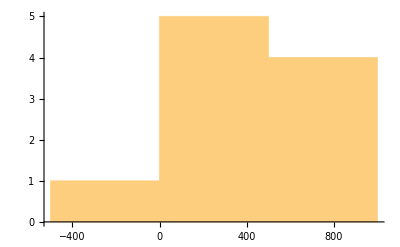

```mathematica
Histogram@Map[First[#]-Last[#]&, hardeasywc]
```

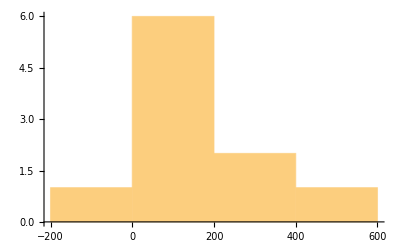

```mathematica
Histogram@Map[First[#]-Last[#]&,<|"worm-health"->{898,627},"immigration-protest"->{876,708},"Indonesian-caveart"->{673,682},"virtual-lab"->{772,692},"england-yeti"->{572,438},"virus-bacteria"->{765,719},"campfire-stories"->{828,652},"drought-inequality"->{962,478},"juice-danger"->{901,755},"marathon-bombs"->{958,626}|> ]
```

```mathematica
sampleFilePath = Map[
	Map[FileNameJoin[{folder, #}]&]@
		{#[["hard", "filename"]], #[["easy", "filename"]]}&
	, sample
	]
```

<|lonewoman-island→{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.4.txt},chinesewomen-cigarettes→{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.4.txt}|>

```mathematica
Map[wordCountFromPath, sampleFilePath]
```

<|lonewoman-island→wordCountFromPath[{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.4.txt}],chinesewomen-cigarettes→wordCountFromPath[{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.4.txt}]|>

```mathematica
WordCount["I am so tired"]
```

4

```mathematica
Map[
	Map[FileNameJoin[{folder, #}]&]@
		{#[["hard", "filename"]], #[["easy", "filename"]]}&
	, sample
	]
```

<|lonewoman-island→{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/lonewoman-island.en.4.txt},chinesewomen-cigarettes→{/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.1.txt,/Users/AaronLopes/Desktop/newsela_article_corpus/articles/chinesewomen-cigarettes.en.4.txt}|>

```mathematica
enMetadata = metadata[Select[#language=="en"&]];
refEasyGrouped = Normal@GroupBy[enMetadata, {#slug&, If[#gradelevel ≤ 6.0, "easy", "hard"]&}];

(* Change second parameter for randlist to select number of random files *)
sample = RandomSample[refEasyGrouped, 2];
sample = Map[RandomChoice, sample, {2}]
```

<|lonewoman-island→<|hard→<|slug→lonewoman-island,language→en,title→Archaeological dig stopped short of solving mystery of the Lone Woman,gradelevel→8.,version→1,filename→lonewoman-island.en.1.txt|>,easy→<|slug→lonewoman-island,language→en,title→The Lone Woman of San Nicolas Island,gradelevel→4.,version→4,filename→lonewoman-island.en.4.txt|>|>,chinesewomen-cigarettes→<|hard→<|slug→chinesewomen-cigarettes,language→en,title→Chinese women on the front lines of the tobacco war,gradelevel→8.,version→1,filename→chinesewomen-cigarettes.en.1.txt|>,easy→<|slug→chinesewomen-cigarettes,language→en,title→China tries to get people to stop smoking,gradelevel→4.,version→4,filename→chinesewomen-cigarettes.en.4.txt|>|>|>

```mathematica
Map[{#[["hard", "filename"]],#[["easy", "filename"]]}&, sample]
```

<|lonewoman-island→{lonewoman-island.en.1.txt,lonewoman-island.en.4.txt},chinesewomen-cigarettes→{chinesewomen-cigarettes.en.1.txt,chinesewomen-cigarettes.en.4.txt}|>

```mathematica
Map[RandomChoice,,{2}]
```

<|recycling-procon→<|hard→<|slug→recycling-procon,language→en,title→PRO/CON: Are U.S. recycling programs too costly?,gradelevel→12.,version→0,filename→recycling-procon.en.0.txt|>,easy→<|slug→recycling-procon,language→en,title→PRO/CON: Should we throw away the recycling program?,gradelevel→6.,version→2,filename→recycling-procon.en.2.txt|>|>,rip-currents→<|hard→<|slug→rip-currents,language→en,title→Scientists study deadly rip currents, hoping to help keep swimmers safe,gradelevel→9.,version→1,filename→rip-currents.en.1.txt|>,easy→<|slug→rip-currents,language→en,title→Scientists hope to help lifeguards save swimmers from deadly rip currents,gradelevel→5.,version→3,filename→rip-currents.en.3.txt|>|>,dog-soldiers→<|hard→<|slug→dog-soldiers,language→en,title→Dogged soldiers: Group honors canines' service to military,gradelevel→12.,version→0,filename→dog-soldiers.en.0.txt|>,easy→<|slug→dog-soldiers,language→en,title→Dog soldiers help Army soldiers,gradelevel→2.,version→5,filename→dog-soldiers.en.5.txt|>|>,code-breaker→<|hard→<|slug→code-breaker,language→en,title→Mavis Batey, code breaker who helped ensure D-Day success, dies at 92,gradelevel→8.,version→1,filename→code-breaker.en.1.txt|>,easy→<|slug→code-breaker,language→en,title→World War II code cracker Mavis Batey dies,gradelevel→5.,version→3,filename→code-breaker.en.3.txt|>|>,unc-cheating→<|hard→<|slug→unc-cheating,language→en,title→Trouble at UNC after report says some classes were fake,gradelevel→7.,version→2,filename→unc-cheating.en.2.txt|>,easy→<|slug→unc-cheating,language→en,title→College classes and grades were fake, now the trouble is real,gradelevel→4.,version→4,filename→unc-cheating.en.4.txt|>|>,compton-talentagents→<|hard→<|slug→compton-talentagents,language→en,title→Talent agents go from A-list to ABCs in school mentors program,gradelevel→12.,version→0,filename→compton-talentagents.en.0.txt|>,easy→<|slug→compton-talentagents,language→en,title→Agents work with movie stars, and some also help kids with homework,gradelevel→3.,version→4,filename→compton-talentagents.en.4.txt|>|>,potus-address→<|hard→<|slug→potus-address,language→en,title→Obama in State of the Union: America is turning the page,gradelevel→12.,version→0,filename→potus-address.en.0.txt|>,easy→<|slug→potus-address,language→en,title→Obama says tax the rich, help the middle class,gradelevel→5.,version→3,filename→potus-address.en.3.txt|>|>,schoollunch-fail→<|hard→<|slug→schoollunch-fail,language→en,title→New nutrition study flunks students' brown-bag lunches,gradelevel→7.,version→2,filename→schoollunch-fail.en.2.txt|>,easy→<|slug→schoollunch-fail,language→en,title→Study takes a look inside a student's lunch box — and gives it an F,gradelevel→4.,version→4,filename→schoollunch-fail.en.4.txt|>|>,baby-chimp→<|hard→<|slug→baby-chimp,language→en,title→Neglected by its mother, baby chimp starts new life in Florida,gradelevel→12.,version→0,filename→baby-chimp.en.0.txt|>,easy→<|slug→baby-chimp,language→en,title→Keeva, the baby chimp, gets to know a new family in a sunny new zoo,gradelevel→3.,version→4,filename→baby-chimp.en.4.txt|>|>,parks-lines→<|hard→<|slug→parks-lines,language→en,title→More theme parks make sure waiting in line is long on fun,gradelevel→12.,version→0,filename→parks-lines.en.0.txt|>,easy→<|slug→parks-lines,language→en,title→Theme parks try to make waiting in line as much fun as the ride,gradelevel→4.,version→4,filename→parks-lines.en.4.txt|>|>|>

```mathematica
enMetadata = metadata[Select[#language=="en"&]];
refEasyGrouped = Normal@GroupBy[enMetadata, {#slug&, #gradelevel ≤ 6.0&}]
```

<|football-helmets→<|False→{<|slug→football-helmets,language→en,title→Can extra padding make football helmets safer?,gradelevel→12.,version→0,filename→football-helmets.en.0.txt|>,<|1|>,<|1|>},True→{1}|>,1909,europe-biking→1|>
 |  |  |  |

```mathematica
hlist
```

{fivesecond-rule,texas-immigrants,dental-dna,mars-curiosity,africa-entrepreneurs,obamalibrary-chicagodecision,testtube-meat,sewage-drinkingwater,oarfish-mystery,elsalvador-gold}

```mathematica
lowtext =Flatten[ Select[lowLevelFileNames,StringStartsQ[#<>".en"]]&/@hlist];
```

```mathematica
lowtext
```

{fivesecond-rule.en.0.txt,fivesecond-rule.en.1.txt,texas-immigrants.en.0.txt,texas-immigrants.en.1.txt,texas-immigrants.en.2.txt,dental-dna.en.0.txt,dental-dna.en.1.txt,dental-dna.en.2.txt,mars-curiosity.en.0.txt,mars-curiosity.en.1.txt,mars-curiosity.en.2.txt,africa-entrepreneurs.en.0.txt,africa-entrepreneurs.en.1.txt,africa-entrepreneurs.en.2.txt,obamalibrary-chicagodecision.en.0.txt,obamalibrary-chicagodecision.en.1.txt,obamalibrary-chicagodecision.en.2.txt,testtube-meat.en.0.txt,testtube-meat.en.1.txt,testtube-meat.en.2.txt,sewage-drinkingwater.en.0.txt,sewage-drinkingwater.en.1.txt,sewage-drinkingwater.en.2.txt,oarfish-mystery.en.0.txt,oarfish-mystery.en.1.txt,elsalvador-gold.en.0.txt,elsalvador-gold.en.1.txt,elsalvador-gold.en.2.txt}

```mathematica
(*simplfiy*)
```

```mathematica
extractStats[filename_]:= {WordCount[Import[StringJoin[folder,filename]]],Length[TextSentences[Import[StringJoin[folder,filename]]]]};
lowmap = AssociationMap[extractStats,lowtext]//Dataset
highmap = AssociationMap[extractStats,hightext]//Dataset
```

Dataset[<>]

Dataset[<>]

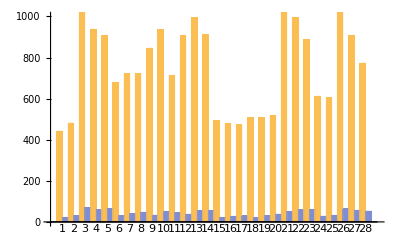
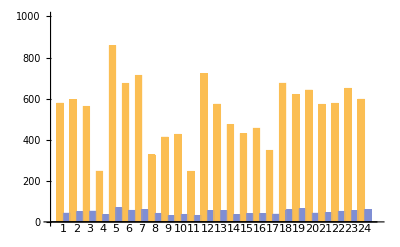

```mathematica
{BarChart[lowmap,ChartLabels->{Range[Length[lowtext]],None},PlotRange->{Automatic,{0,1000}}],BarChart[highmap,ChartLabels->{Range[Length[hightext]],None},PlotRange->{Automatic,{0,1000}}]}
```

```mathematica
lowsentences = TextSentences[randCorpusLow[[1;;3]],5]
highsentences = TextSentences[randCorpusHigh[[1;;3]],5]
```

{{A new study appears to validate what every 12-year-old knows: If you drop food on the floor, you have five seconds until it becomes contaminated.,Biology students at Aston University in Birmingham, England, tested the time-honored five-second rule and claim to have found some truth to it.,The faster you pick food up off the floor, they discovered, the less likely it is to contain bacteria.,Working under the direction of microbiology professor Anthony Hilton, the students dropped toast, pasta, cookies and sticky candy and left them on the floor for three to 30 seconds, according to information released on the university's website March 10.,They then monitored the transfer of two common bacteria, Escherichia coli and Staphylococcus aureus — in common terms, E.coli and staph.},{A new study appears to prove what every 12-year-old knows: If you drop food on the floor, you have five seconds until it becomes contaminated with bacteria that could give you food poisoning.,Students at Aston University in Birmingham, England, tested the age-old five-second rule and claim to have found some truth to it.,The faster you pick food up off the floor, they discovered, the less likely it is to contain bacteria.,Working under the direction of professor Anthony Hilton, the students dropped toast, pasta, cookies and sticky candy on the floor.,Then they left the food on the floor for three to 30 seconds, according to information released on the university's website on March 10.},{HOUSTON, Texas — A year ago, the Las Americas Newcomer Middle School in the low-income Gulfton neighborhood started the semester with 150 immigrant and refugee students.,When the new school year began last month, enrollment skyrocketed to 325 students, most of them newly arrived from Central America.,"It's put a burden on me because I've run out of space," Principal Maria Moreno said of the school's dozen portable classrooms set up behind another middle school.,She hired five new teachers and a social worker, converted a teachers lounge and school police office into classrooms and used surplus money to buy projectors, laptops and desktop computers.,But she still had to turn away more than 100 students.}}

{{Have you ever heard of the five second rule?,It's an old belief about dropping food on the floor and having five seconds to pick it up.,The rule says that if you wait longer than five seconds then you shouldn't eat it.,Recently, science students at Aston University in England tested the age-old five-second rule.,They claim to have found some truth to it.},{Have you ever heard of the five-second rule?,It's an old belief about dropping food on the floor and having five seconds to pick it up.,The rule says that if you wait longer than five seconds, then you shouldn't eat it.,Recently, science students at Aston University in England tested the five-second rule.,They claim to have found some truth to it.},{Have you ever heard of the five-second rule?,It's an old belief about dropping food on the floor and having five seconds to pick it up.,The rule says that if you wait longer than five seconds then you shouldn't eat it.,If you do, you might get sick.,Not long ago scientists in England tested the rule.}}